```mathematica
Calculating the average V values
```

```mathematica
all=Import["C:\\Users\\Peggy\\Desktop\\transport properties of copper\\data\\electro27.txt", "Table"];
```

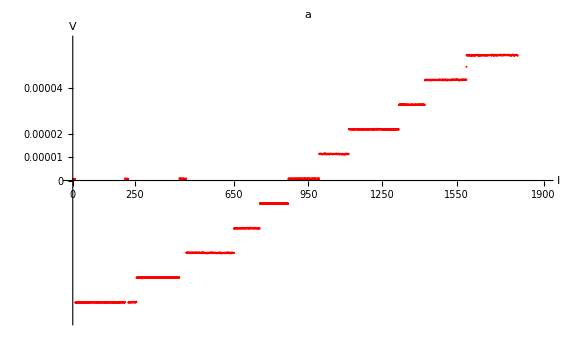

```mathematica
a=ListPlot[all,PlotMarkers->{Automatic, 2}, PlotStyle->{Red} , PlotRange->{{0,1900}, {-0.00006,0.00006}} ,
 AxesLabel->{" I", " V"}, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"a" ,Ticks->{{0,100,250,500,650,800,950,1100,1250,1400,1550,1750,1900},{0,0.00001,0.00002,0.00004,0.00007,0.00009,0.00012}}]
```

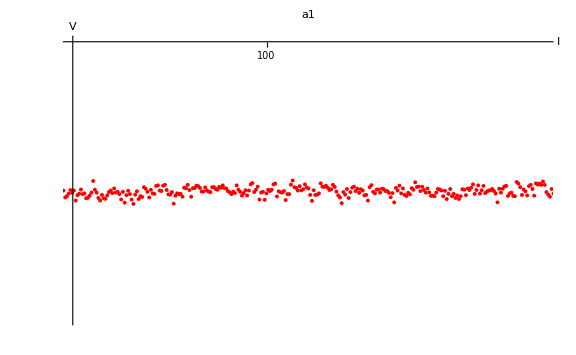

```mathematica
a1=ListPlot[all,PlotMarkers->{Automatic, 4}, PlotStyle->{Red} , PlotRange->{{30,200}, {-0.000055,-0.00005}} ,
 AxesLabel->{" I", " V"}, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"a1" ,Ticks->{{0,20,100,200,500,650,800,950,1100,1250,1400,1550,1750,1900},{-0.00006,-0.00005,-0.00004, 0.00001,0.00002,0.00004,0.00007,0.00009,0.00012}}]
```

```mathematica
a11=List[{30.419,-0.0000526805153},{31.051,-0.0000528614899},{31.683,-0.0000527641206},{32.314,-0.0000527363008},{32.945,-0.0000526621147},{33.577,-0.0000527455741},{34.208,-0.0000527316795},{34.839,-0.0000528197755},{35.471,-0.0000528105023},{36.103,-0.0000527734092},{36.735,-0.00005271769},{37.367,-0.0000525090418},{37.998,-0.0000526666871},{38.63,-0.00005271769},{39.262,-0.0000528150592},{39.894,-0.0000528615072},{40.526,-0.0000527595013},{41.158,-0.0000528197775},{41.79,-0.0000528290508},{42.422,-0.0000527686977},{43.054,-0.0000527084216},{43.686,-0.0000526806018},{44.318,-0.0000527269681},{44.95,-0.0000526435088},{45.582,-0.0000527176333},{46.214,-0.0000527037235},{46.846,-0.0000527454531},{47.476,-0.0000528428221},{48.108,-0.0000527037695},{48.74,-0.0000528985078},{49.372,-0.0000527640457},{50.004,-0.000052685223},{50.636,-0.0000527454992},{51.269,-0.0000528428876},{51.901,-0.0000529217102},{52.533,-0.0000527547917},{53.165,-0.0000526945155},{53.797,-0.0000528335993},{54.429,-0.0000527825964},{55.061,-0.0000527965063},{55.693,-0.0000526203145},{56.325,-0.0000526481343},{56.957,-0.0000527037429},{57.589,-0.0000528057486},{58.221,-0.0000526666499},{58.853,-0.0000527315626},{59.485,-0.0000527408399},{60.117,-0.0000525971046},{60.749,-0.0000525878314},{61.381,-0.0000526805638},{62.013,-0.0000526898371},{62.645,-0.000052592521},{63.277,-0.0000525786111},{63.909,-0.0000526713437},{64.541,-0.0000527501663},{65.173,-0.0000527548194},{65.805,-0.0000527084531},{66.437,-0.0000529171014},{67.069,-0.0000527733659},{67.701,-0.0000527316193},{68.333,-0.0000527455291},{68.965,-0.0000527408925},{69.597,-0.0000527918954},{70.229,-0.0000526296135},{70.861,-0.0000526389208},{71.493,-0.0000525786446},{72.125,-0.0000526713772},{72.757,-0.0000527919296},{73.389,-0.0000526388968},{74.021,-0.0000526342602},{74.653,-0.0000525925305},{75.285,-0.0000526018038},{75.917,-0.0000526342602},{76.549,-0.0000526990736},{77.181,-0.0000526990736},{77.813,-0.0000526248877},{78.445,-0.0000526805271},{79.077,-0.0000526991464},{79.709,-0.0000527084196},{80.341,-0.0000526203237},{80.973,-0.0000526203237},{81.605,-0.0000526527801},{82.237,-0.0000526667824},{82.869,-0.0000526157794},{83.501,-0.0000526296893},{84.133,-0.0000525879596},{84.765,-0.0000526388387},{85.397,-0.0000526434754},{86.029,-0.0000526898416},{86.661,-0.0000527130247},{87.293,-0.0000527454811},{87.925,-0.0000526991291},{88.557,-0.0000527269488},{89.189,-0.0000525878501},{89.821,-0.0000526666727},{90.453,-0.0000527038451},{91.085,-0.0000527733946},{91.717,-0.0000527270283},{92.349,-0.0000526760253},{92.981,-0.000052768758},{93.613,-0.000052680615},{94.245,-0.0000525693359},{94.877,-0.0000525461528},{95.509,-0.0000527084348},{96.141,-0.000052666634},{96.773,-0.0000526109945},{97.405,-0.0000528428256},{98.037,-0.0000527176368},{98.669,-0.000052703727},{99.301,-0.0000528474674},{99.933,-0.0000527315519},{100.565,-0.0000526666392},{101.198,-0.0000526898223},{101.83,-0.0000526667129},{102.462,-0.0000525693438},{103.094,-0.0000525554339},{103.727,-0.0000527872653},{104.359,-0.0000526945327},{104.991,-0.0000527130966},{105.623,-0.0000527177332},{106.255,-0.0000526899134},{106.887,-0.0000528521955},{107.519,-0.0000527454782},{108.151,-0.0000527454782},{108.783,-0.0000525739232},{109.415,-0.0000524997372},{110.047,-0.0000526202894},{110.679,-0.000052634125},{111.285,-0.0000526804912},{111.943,-0.0000526016687},{112.575,-0.0000526758546},{113.207,-0.0000526573763},{113.839,-0.0000525692805},{114.471,-0.00005262492},{115.103,-0.0000526434665},{115.735,-0.000052759382},{116.367,-0.0000528660537},{116.999,-0.0000526759521},{117.605,-0.0000527594114},{118.263,-0.0000527547747},{118.895,-0.0000527316542},{119.527,-0.0000525508256},{120.159,-0.0000526111018},{120.791,-0.0000526157384},{121.423,-0.0000525925265},{122.055,-0.0000526296196},{122.687,-0.0000526713492},{123.319,-0.0000526574393},{123.951,-0.0000525786167},{124.583,-0.000052615612},{125.215,-0.0000526990712},{125.847,-0.0000527686205},{126.479,-0.0000528057134},{127.111,-0.0000529077894},{127.743,-0.0000527084145},{128.375,-0.0000527547808},{129.007,-0.000052652775},{129.639,-0.0000528150569},{130.271,-0.0000527084429},{130.903,-0.0000526296202},{131.535,-0.0000526110737},{132.167,-0.0000526898964},{132.799,-0.0000526481928},{133.431,-0.0000527223789},{134.063,-0.0000526574661},{134.695,-0.0000526806492},{135.327,-0.0000527687452},{135.959,-0.0000527595161},{136.591,-0.0000528615221},{137.223,-0.0000526204171},{137.855,-0.000052583324},{138.487,-0.0000527038078},{139.119,-0.0000527316276},{139.751,-0.0000526620781},{140.383,-0.0000526620781},{141.015,-0.0000527177177},{141.647,-0.0000526481128},{142.279,-0.000052657386},{142.911,-0.0000526898424},{143.543,-0.0000526898424},{144.175,-0.0000527223584},{144.807,-0.0000528011811},{145.439,-0.000052726995},{146.071,-0.0000528939136},{146.703,-0.0000526342624},{147.335,-0.0000526806515},{147.967,-0.0000525925555},{148.599,-0.0000527316544},{149.231,-0.0000526435584},{149.863,-0.0000527593921},{150.495,-0.0000527779385},{151.127,-0.0000527222991},{151.759,-0.0000527501188},{152.391,-0.0000526388398},{153.023,-0.0000526666589},{153.656,-0.0000525321969},{154.288,-0.0000526156561},{154.92,-0.0000526110195},{155.552,-0.0000526898658},{156.184,-0.0000526110432},{156.816,-0.0000526713193},{157.448,-0.0000527176856},{158.08,-0.0000526434995},{158.712,-0.0000527129758},{159.344,-0.0000527778885},{159.976,-0.0000527732519},{160.608,-0.0000527825251},{161.24,-0.0000527175816},{161.872,-0.000052652669},{162.504,-0.0000526619422},{163.134,-0.0000526804887},{163.766,-0.0000527824943},{164.398,-0.0000526850403},{165.03,-0.0000528334118},{165.663,-0.0000527406796},{166.295,-0.000052652584},{166.927,-0.0000527824116},{167.559,-0.0000527406821},{168.191,-0.0000528148679},{168.823,-0.0000527685018},{169.455,-0.0000528335272},{170.087,-0.0000527825244},{170.719,-0.0000526573357},{171.351,-0.0000526666089},{171.983,-0.0000527639779},{172.615,-0.0000526434444},{173.247,-0.0000526712641},{173.879,-0.0000526295346},{174.511,-0.0000525692585},{175.143,-0.0000527408652},{175.775,-0.0000526713158},{176.407,-0.0000525878565},{177.039,-0.0000527362285},{177.671,-0.0000526759524},{178.303,-0.0000525971948},{178.935,-0.0000527270205},{179.567,-0.0000526992007},{180.199,-0.0000526806542},{180.831,-0.0000526760028},{181.463,-0.0000526528196},{182.095,-0.0000526899126},{182.727,-0.0000527362789},{183.359,-0.0000528939244},{183.991,-0.0000526482093},{184.623,-0.0000527177588},{185.255,-0.0000526482093},{185.887,-0.0000526064796},{186.519,-0.0000525971965},{187.151,-0.0000527780252},{187.783,-0.0000527316588},{188.415,-0.000052717749},{189.047,-0.0000527780252},{189.679,-0.0000527825828},{190.311,-0.0000525275685},{190.943,-0.0000525553882},{191.575,-0.000052620301},{192.207,-0.0000527594168},{192.839,-0.0000526620477},{193.471,-0.000052694504},{194.103,-0.00005276869},{194.735,-0.0000526017715},{195.367,-0.0000525785991},{195.999,-0.0000526527851},{196.631,-0.0000527733374},{197.263,-0.0000525507793},{197.895,-0.0000525739071},{198.525,-0.0000525553606},{199.157,-0.0000525785437},{199.789,-0.0000525182676},{200.421,-0.0000525785437}];
Mean[a11]
```

{115.418,-0.0000526958}

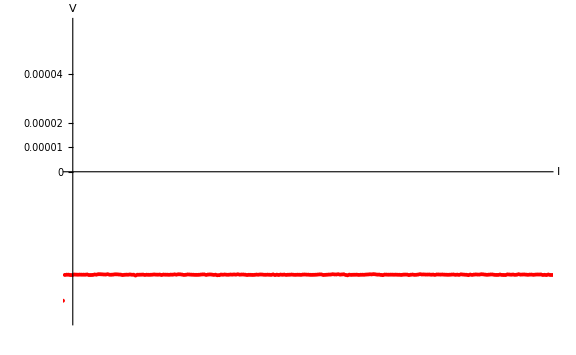

```mathematica
a2=ListPlot[all,PlotMarkers->{Automatic, 4}, PlotStyle->{Red} , PlotRange->{{260,420}, {-0.00006,0.0000601}} ,
 AxesLabel->{" I", " V"}, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"" ,Ticks->{{0,100,250,500,650,800,950,1100,1250,1400,1550,1750,1900},{0,0.00001,0.00002,0.00004,0.00007,0.00009,0.00012}}]
```

```mathematica
a22=List[{260.464,-0.0000418958229},{261.096,-0.0000419375525},{261.728,-0.0000419700089},{262.36,-0.0000419329159},{262.992,-0.0000419607166},{263.624,-0.0000419607166},{264.256,-0.0000419653532},{264.888,-0.000041881894},{265.52,-0.0000420998154},{266.152,-0.000042090524},{266.785,-0.000042053431},{267.417,-0.0000418818759},{268.049,-0.0000419514253},{268.681,-0.0000417706268},{269.313,-0.0000417845366},{269.945,-0.0000418262663},{270.577,-0.0000418819058},{271.209,-0.000041905089},{271.841,-0.0000417659927},{272.473,-0.0000419653677},{273.105,-0.000041974641},{273.737,-0.0000419143648},{274.369,-0.0000418170605},{275.001,-0.0000418263338},{275.633,-0.00004188661},{276.265,-0.000041937613},{276.897,-0.0000420952533},{277.529,-0.0000420117939},{278.161,-0.0000419515176},{278.791,-0.0000419700642},{279.423,-0.0000418773315},{280.055,-0.0000419699751},{280.687,-0.0000419746117},{281.319,-0.0000422899022},{281.951,-0.000041983885},{282.584,-0.0000419746234},{283.216,-0.0000419514403},{283.848,-0.0000419236205},{284.48,-0.0000420534461},{285.112,-0.0000419699868},{285.744,-0.0000420117638},{286.376,-0.0000420024906},{287.008,-0.0000419561243},{287.64,-0.0000418773016},{288.272,-0.0000419375851},{288.904,-0.0000419607683},{289.536,-0.000041914402},{290.168,-0.0000420766841},{290.8,-0.0000419190386},{291.432,-0.0000419607305},{292.065,-0.0000419653671},{292.697,-0.0000420024602},{293.329,-0.0000419375474},{293.961,-0.0000419560689},{294.594,-0.00004183088},{295.223,-0.0000419560689},{295.855,-0.0000418030603},{296.487,-0.0000418262434},{297.119,-0.0000419143326},{297.751,-0.0000420534313},{298.383,-0.0000420070651},{299.015,-0.0000418633297},{299.647,-0.0000419004559},{300.279,-0.0000419560955},{300.911,-0.0000419792786},{301.543,-0.0000420210082},{302.175,-0.0000420256449},{302.807,-0.000042007115},{303.439,-0.0000419282923},{304.071,-0.0000418541062},{304.703,-0.0000418541062},{305.335,-0.0000420488439},{305.967,-0.0000419143816},{306.599,-0.0000418680153},{307.231,-0.0000419143816},{307.863,-0.000042034934},{308.495,-0.0000419654157},{309.127,-0.0000421740641},{309.759,-0.0000421416077},{310.391,-0.0000419190493},{311.023,-0.0000419653925},{311.655,-0.0000418912064},{312.287,-0.0000419793023},{312.92,-0.0000419932122},{313.552,-0.0000419004796},{314.184,-0.0000419375195},{314.816,-0.0000418726068},{315.448,-0.0000419375195},{316.08,-0.0000417984208},{316.712,-0.0000419514265},{317.344,-0.0000419004237},{317.976,-0.000041895787},{318.608,-0.000041969973},{319.24,-0.000042081252},{319.872,-0.000042002416},{320.504,-0.0000420209625},{321.136,-0.0000420580555},{321.768,-0.0000420255991},{322.4,-0.0000419236287},{323.032,-0.0000419746316},{323.664,-0.0000418818991},{324.296,-0.0000418958089},{324.928,-0.0000419792682},{325.56,-0.0000420024887},{326.192,-0.0000419468491},{326.824,-0.0000419932154},{327.456,-0.0000420210352},{328.088,-0.0000418633893},{328.72,-0.0000420952208},{329.352,-0.0000419561219},{329.984,-0.0000420720376},{330.616,-0.0000419190076},{331.248,-0.0000419885571},{331.854,-0.0000419190076},{332.512,-0.0000420488332},{333.144,-0.0000419839204},{333.776,-0.0000419699667},{334.408,-0.0000419096906},{335.04,-0.0000419885132},{335.672,-0.0000420209696},{336.304,-0.0000419700085},{336.936,-0.0000419839184},{337.568,-0.0000420163748},{338.2,-0.0000419190056},{338.832,-0.0000418911858},{339.464,-0.0000419468527},{340.096,-0.0000419607626},{340.728,-0.0000420210388},{341.36,-0.0000420210388},{341.992,-0.0000420025068},{342.624,-0.000041974687},{343.256,-0.0000419144108},{343.888,-0.0000418402247},{344.52,-0.0000418634079},{345.152,-0.0000420767054},{345.784,-0.0000420210658},{346.416,-0.0000419700628},{347.048,-0.0000419097865},{347.68,-0.0000419050954},{348.312,-0.0000417799065},{348.944,-0.0000418633658},{349.576,-0.0000418819123},{350.208,-0.0000417799065},{350.84,-0.0000419329295},{351.472,-0.0000418726533},{352.104,-0.0000418077405},{352.736,-0.0000420627551},{353.368,-0.0000421972252},{354.,-0.0000419561204},{354.633,-0.0000420256699},{355.265,-0.0000419885768},{355.897,-0.0000419793036},{356.529,-0.0000419561307},{357.161,-0.0000420488634},{357.793,-0.0000419932238},{358.425,-0.0000419793139},{359.057,-0.0000419885704},{359.689,-0.0000419097477},{360.321,-0.0000418772913},{360.953,-0.0000418077419},{361.585,-0.0000418448349},{362.217,-0.0000417474531},{362.849,-0.0000418262758},{363.481,-0.0000419375548},{364.113,-0.000041923645},{364.745,-0.0000420442176},{365.377,-0.000042127677},{366.009,-0.0000419190286},{366.641,-0.0000419375751},{367.273,-0.0000419746682},{367.905,-0.0000419467922},{368.537,-0.0000419467922},{369.169,-0.0000419699754},{369.801,-0.0000419467922},{370.433,-0.0000419885126},{371.065,-0.0000419977859},{371.697,-0.0000420487887},{372.329,-0.0000419421464},{372.935,-0.0000419143266},{373.593,-0.0000419281803},{374.226,-0.0000421090084},{374.858,-0.0000419838197},{375.49,-0.0000419003606},{376.122,-0.0000420301506},{376.754,-0.0000419976944},{377.386,-0.0000419003255},{378.018,-0.0000417705003},{378.65,-0.0000418818553},{379.282,-0.0000418633088},{379.914,-0.0000419143116},{380.546,-0.000041909675},{381.178,-0.0000418911285},{381.81,-0.0000419700516},{382.442,-0.0000419236853},{383.074,-0.0000420349645},{383.706,-0.0000418819556},{384.338,-0.0000418819005},{384.97,-0.0000419282668},{385.602,-0.0000418865371},{386.234,-0.0000419468133},{386.866,-0.0000419699964},{387.498,-0.0000420023046},{388.13,-0.0000419744849},{388.762,-0.0000419188456},{389.394,-0.0000418817527},{390.026,-0.0000420116869},{390.658,-0.0000419421376},{391.29,-0.0000420255968},{391.922,-0.0000418308587},{392.554,-0.0000418957714},{393.186,-0.0000419607316},{393.818,-0.0000419978246},{394.448,-0.0000421322868},{395.08,-0.0000419143653},{395.712,-0.0000420348458},{396.344,-0.0000419282035},{396.976,-0.0000418632909},{397.608,-0.0000419189303},{398.24,-0.0000419189303},{398.872,-0.0000417798801},{399.505,-0.0000418401563},{400.138,-0.0000419375254},{400.77,-0.0000420070748},{401.402,-0.0000419515078},{402.034,-0.0000418773217},{402.666,-0.0000418773217},{403.298,-0.0000420164207},{403.93,-0.0000420535137},{404.562,-0.0000420442128},{405.194,-0.0000419051139},{405.826,-0.0000420442128},{406.458,-0.0000420813058},{407.09,-0.0000420952229},{407.722,-0.0000418494815},{408.354,-0.000041905121},{408.986,-0.0000419653972},{409.618,-0.000041905121},{410.25,-0.0000420164976},{410.882,-0.0000419701312},{411.514,-0.0000417753923},{412.146,-0.0000419376747},{412.776,-0.0000419052659},{413.408,-0.000041877446},{414.04,-0.000041942359},{414.672,-0.0000420072721},{415.304,-0.0000419330857},{415.936,-0.0000419191343},{416.569,-0.0000420165038},{417.202,-0.0000419330443},{417.834,-0.0000418866778},{418.466,-0.0000419004991},{419.098,-0.000041877316},{419.73,-0.0000420674179}];
Mean[a22]
```

{340.096,-0.0000419496}

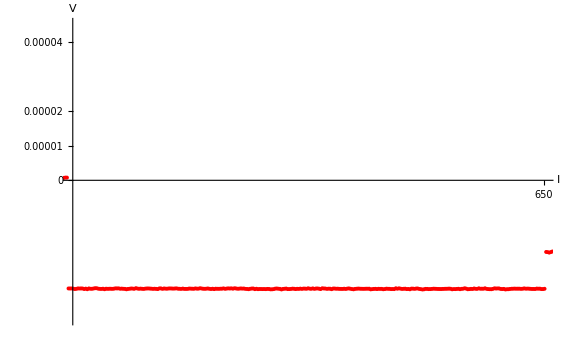

```mathematica
a3=ListPlot[all,PlotMarkers->{Automatic, 4}, PlotStyle->{Red} , PlotRange->{{460,650}, {-0.00004,0.000045}} ,
 AxesLabel->{" I", " V"}, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"" ,Ticks->{{0,100,250,500,650,800,950,1100,1250,1400,1550,1750,1900},{0,0.00001,0.00002,0.00004,0.00007,0.00009,0.00012}},AxesOrigin->{{0},{-0,00006}}]
```

```mathematica
a33=List[{459.546,-0.0000312084159},{460.178,-0.0000312547822},{460.81,-0.0000313706666},{461.442,-0.0000313103905},{462.074,-0.0000311991114},{462.706,-0.0000312222946},{463.338,-0.0000312083847},{463.97,-0.0000312176765},{464.602,-0.0000313706853},{465.234,-0.000031250133},{465.866,-0.0000314309615},{466.498,-0.000031199079},{467.13,-0.000031296448},{467.762,-0.000031296448},{468.394,-0.0000312222621},{469.026,-0.0000311388029},{469.658,-0.0000311480877},{470.29,-0.0000312732766},{470.922,-0.0000313150062},{471.554,-0.0000313381893},{472.186,-0.0000312779839},{472.818,-0.0000314309928},{473.45,-0.0000312779839},{474.082,-0.000031315077},{474.714,-0.0000312872572},{475.346,-0.0000312872375},{475.978,-0.0000313150572},{476.61,-0.0000312686909},{477.242,-0.0000311759583},{477.874,-0.0000312037458},{478.507,-0.0000311805627},{479.139,-0.0000312918417},{479.771,-0.0000312501121},{480.403,-0.0000313057599},{481.035,-0.0000313196698},{481.667,-0.0000314494954},{482.299,-0.0000313382163},{482.931,-0.00003129185},{483.563,-0.0000312177141},{484.195,-0.0000312455339},{484.827,-0.0000313104468},{485.459,-0.0000311249814},{486.091,-0.0000312362706},{486.723,-0.0000312965469},{487.355,-0.0000312501805},{487.987,-0.0000313011835},{488.619,-0.0000313382766},{489.251,-0.0000312548031},{489.883,-0.00003121771},{490.515,-0.0000312084367},{491.147,-0.0000312408932},{491.779,-0.0000312733566},{492.411,-0.0000313150863},{493.043,-0.0000312826299},{493.675,-0.000031319723},{494.307,-0.0000313846359},{494.939,-0.0000311898822},{495.571,-0.0000311945189},{496.203,-0.0000313150713},{496.835,-0.0000312084288},{497.467,-0.0000312640516},{498.099,-0.0000312779615},{498.731,-0.0000312084121},{499.363,-0.0000312037754},{499.995,-0.0000312269586},{500.627,-0.0000312547256},{501.259,-0.0000312176326},{501.891,-0.0000311851763},{502.523,-0.0000312825453},{503.155,-0.000031296461},{503.787,-0.0000313242807},{504.419,-0.0000312408215},{505.051,-0.0000313381906},{505.683,-0.0000313289173},{506.315,-0.0000313289464},{506.947,-0.0000312315772},{507.579,-0.0000312547603},{508.212,-0.0000312779435},{508.845,-0.0000313011229},{509.477,-0.0000311944805},{510.107,-0.0000312640299},{510.739,-0.0000312640299},{511.371,-0.0000311481142},{512.003,-0.000031222323},{512.635,-0.0000312872358},{513.267,-0.0000313057823},{513.899,-0.0000312733259},{514.531,-0.0000312130259},{515.163,-0.0000313011218},{515.795,-0.0000313613979},{516.427,-0.0000312825753},{517.059,-0.000031398491},{517.691,-0.0000312733064},{518.323,-0.0000313011261},{518.955,-0.0000313057627},{519.587,-0.000031277943},{520.219,-0.0000312733385},{520.851,-0.0000311852425},{521.483,-0.0000313104316},{522.115,-0.0000312362455},{522.747,-0.0000311852425},{523.379,-0.0000312269653},{524.011,-0.0000311759623},{524.643,-0.0000312733316},{525.275,-0.0000311481425},{525.907,-0.0000312130423},{526.539,-0.0000312872284},{527.171,-0.0000312594086},{527.803,-0.0000312037691},{528.435,-0.0000312501353},{529.067,-0.0000312269629},{529.699,-0.0000313243322},{530.332,-0.0000313475153},{530.964,-0.0000314217014},{531.596,-0.0000313011797},{532.228,-0.0000312316302},{532.86,-0.0000312223569},{533.492,-0.000031412459},{534.124,-0.0000312918901},{534.756,-0.0000314124426},{535.388,-0.0000313614396},{536.02,-0.0000313707129},{536.652,-0.0000313892594},{537.284,-0.0000313706438},{537.916,-0.0000314077368},{538.548,-0.0000313381874},{539.18,-0.0000313520973},{539.812,-0.0000314633659},{540.444,-0.000031449456},{541.076,-0.0000313984532},{541.708,-0.0000312593545},{542.34,-0.0000312222616},{542.972,-0.0000312825962},{543.604,-0.0000313196892},{544.236,-0.0000314958812},{544.868,-0.0000313335991},{545.5,-0.0000312918442},{546.132,-0.0000312362047},{546.764,-0.00003139385},{547.396,-0.0000313845768},{548.028,-0.0000313382105},{548.66,-0.0000312594017},{549.292,-0.0000312918581},{549.924,-0.0000313845907},{550.556,-0.0000313011314},{551.188,-0.0000313336266},{551.82,-0.0000312501671},{552.452,-0.0000313243533},{553.084,-0.0000312408939},{553.716,-0.0000312501671},{554.346,-0.0000313011365},{554.976,-0.0000311620377},{555.609,-0.0000312640435},{556.241,-0.0000313011365},{556.873,-0.000031189843},{557.505,-0.0000313196686},{558.137,-0.000031226936},{558.769,-0.0000312083895},{559.401,-0.0000312733023},{560.033,-0.0000313845859},{560.665,-0.0000311573911},{561.297,-0.0000312176673},{561.929,-0.0000312269405},{562.561,-0.0000313197002},{563.193,-0.0000312686972},{563.825,-0.0000312733338},{564.457,-0.0000314170694},{565.089,-0.0000312316042},{565.721,-0.0000312316344},{566.353,-0.0000312919107},{566.985,-0.0000312687275},{567.617,-0.0000313243671},{568.249,-0.0000313243789},{568.881,-0.0000313429255},{569.513,-0.0000312780125},{570.145,-0.0000313475621},{570.777,-0.0000312548293},{571.409,-0.000031194483},{572.041,-0.0000312872155},{572.673,-0.0000313753114},{573.306,-0.0000314541341},{573.938,-0.0000313242819},{574.57,-0.0000312871889},{575.202,-0.0000312408227},{575.834,-0.000031273279},{576.466,-0.0000313010988},{577.098,-0.0000313057573},{577.73,-0.0000313103939},{578.362,-0.0000312779375},{578.994,-0.0000312872108},{579.626,-0.0000312733092},{580.258,-0.0000314680476},{580.89,-0.0000313984982},{581.522,-0.0000313335854},{582.154,-0.0000313104022},{582.786,-0.0000313845869},{583.418,-0.0000313011276},{584.051,-0.0000313243108},{584.683,-0.0000313196742},{585.315,-0.0000314355963},{585.947,-0.0000313799567},{586.579,-0.0000312686776},{587.211,-0.000031301134},{587.843,-0.0000313150279},{588.475,-0.0000313892139},{589.107,-0.0000313660308},{589.739,-0.0000313984871},{590.371,-0.0000311527459},{591.003,-0.0000312871767},{591.635,-0.0000311712612},{592.267,-0.000031259357},{592.899,-0.0000313381796},{593.531,-0.0000313011108},{594.163,-0.0000312686544},{594.795,-0.0000313892067},{595.427,-0.0000313521137},{596.059,-0.0000314494828},{596.691,-0.000031250115},{597.323,-0.0000312593883},{597.955,-0.0000313196644},{598.587,-0.0000312315685},{599.219,-0.0000312176573},{599.851,-0.0000313428463},{600.483,-0.000031407759},{601.115,-0.0000315051282},{601.747,-0.0000314494887},{602.379,-0.0000313242633},{603.011,-0.0000313288999},{603.643,-0.0000313984492},{604.275,-0.000031389176},{604.907,-0.0000313381819},{605.539,-0.0000312779058},{606.171,-0.0000312918157},{606.803,-0.0000313242721},{607.435,-0.0000313474552},{608.067,-0.0000313613958},{608.699,-0.000031370669},{609.331,-0.000031333576},{609.963,-0.0000313150295},{610.595,-0.0000312964752},{611.227,-0.0000312918386},{611.859,-0.000031250109},{612.491,-0.0000312964752},{613.123,-0.0000314494839},{613.755,-0.0000313845944},{614.387,-0.0000313985043},{615.019,-0.0000313428648},{615.651,-0.0000312964985},{616.283,-0.0000314217531},{616.915,-0.0000313151105},{617.547,-0.000031282654},{618.179,-0.0000311574647},{618.811,-0.0000312641074},{619.443,-0.000031435641},{620.075,-0.0000313939113},{620.707,-0.0000313197252},{621.339,-0.0000313568182},{621.971,-0.0000312130586},{622.603,-0.0000313057913},{623.235,-0.0000313243378},{623.867,-0.0000311620557},{624.499,-0.0000312918814},{625.131,-0.0000312733297},{625.763,-0.0000312872396},{626.395,-0.0000311574139},{627.027,-0.0000313243326},{627.659,-0.0000313892176},{628.292,-0.0000314170373},{628.923,-0.0000314263106},{629.555,-0.0000313289414},{630.187,-0.0000311666595},{630.819,-0.0000312315762},{631.451,-0.0000311991198},{632.083,-0.0000312083931},{632.715,-0.0000313474919},{633.347,-0.0000313799413},{633.979,-0.0000313289384},{634.611,-0.0000314958569},{635.243,-0.0000314309442},{635.875,-0.000031421692},{636.507,-0.0000313428693},{637.139,-0.0000312918663},{637.771,-0.0000312779564},{638.403,-0.0000312547733},{639.035,-0.0000312825764},{639.667,-0.0000312686665},{640.299,-0.0000312733031},{640.931,-0.0000313150327},{641.563,-0.000031287218},{642.195,-0.0000311898488},{642.827,-0.0000312779448},{643.459,-0.000031250125},{644.091,-0.0000312640349},{644.723,-0.0000313150547},{645.355,-0.0000313475111},{645.987,-0.0000313475111},{646.619,-0.000031361421},{647.251,-0.000031240875},{647.883,-0.0000312779681},{648.515,-0.0000312640582},{649.147,-0.000031379974},{649.779,-0.000031379974},{650.411,-0.0000313011582}];
Mean[a33]
```

{554.979,-0.000031297}

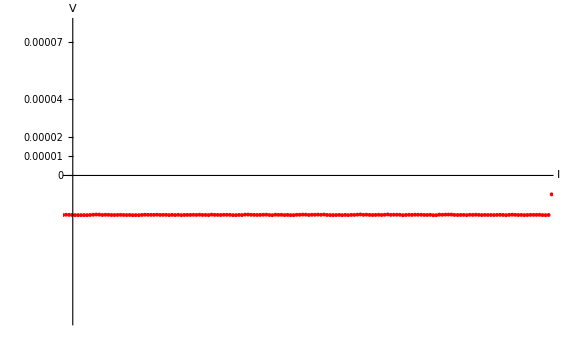

```mathematica
a4=ListPlot[all,PlotMarkers->{Automatic, 4}, PlotStyle->{Red} , PlotRange->{{655,753}, {-0.000075,0.000079}} ,
 AxesLabel->{" I", " V"}, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"" ,Ticks->{{0,100,250,500,650,800,950,1100,1250,1400,1550,1750,1900},{0,0.00001,0.00002,0.00004,0.00007,0.00009,0.00012}},AxesOrigin->{{0},{-0,00006}}]
```

```mathematica
a44=List[{655.467,-0.0000207342504},{656.099,-0.0000207435123},{656.731,-0.0000207296024},{657.363,-0.000020734239},{657.995,-0.0000207435123},{658.627,-0.0000206554575},{659.259,-0.000020534905},{659.891,-0.0000204421723},{660.523,-0.0000204885387},{661.155,-0.0000206600941},{661.787,-0.000020553442},{662.419,-0.0000205812618},{663.051,-0.0000206786311},{663.683,-0.0000206879044},{664.315,-0.0000206368775},{664.947,-0.0000205997845},{665.579,-0.0000206600607},{666.211,-0.0000207017903},{666.843,-0.0000206461508},{667.475,-0.0000207574711},{668.107,-0.000020720378},{668.739,-0.0000207342879},{669.371,-0.0000206322819},{670.003,-0.0000205488483},{670.635,-0.0000205813047},{671.267,-0.0000206137612},{671.899,-0.000020590578},{672.531,-0.0000205303017},{673.163,-0.0000206322557},{673.795,-0.0000206183458},{674.427,-0.0000205997993},{675.059,-0.0000207157151},{675.691,-0.0000206090204},{676.323,-0.0000206971162},{676.955,-0.0000205858373},{677.587,-0.0000207388457},{678.219,-0.00002065075},{678.851,-0.0000206275756},{679.483,-0.0000206322122},{680.115,-0.000020585846},{680.747,-0.0000206368488},{681.379,-0.0000205348589},{682.011,-0.0000206461379},{682.643,-0.0000206368647},{683.275,-0.0000207203239},{683.907,-0.0000204792194},{684.539,-0.0000205951635},{685.171,-0.0000206276199},{685.803,-0.0000206693495},{686.435,-0.0000205766169},{687.067,-0.0000205812468},{687.699,-0.0000206090665},{688.331,-0.0000207296189},{688.963,-0.0000207481654},{689.595,-0.0000206461577},{690.227,-0.0000206878874},{690.859,-0.0000204746025},{691.491,-0.0000204699658},{692.123,-0.0000205766083},{692.755,-0.0000206090877},{693.387,-0.0000206461808},{694.019,-0.000020618361},{694.651,-0.0000205488115},{695.283,-0.0000204932244},{695.915,-0.0000206647802},{696.547,-0.0000207575131},{697.179,-0.0000205164076},{697.811,-0.0000206091405},{698.443,-0.0000205766649},{699.075,-0.0000207111275},{699.707,-0.0000206183946},{700.339,-0.0000207343107},{700.971,-0.0000207388957},{701.603,-0.0000205766137},{702.235,-0.0000205580672},{702.867,-0.0000204746079},{703.499,-0.0000204885177},{704.131,-0.0000206647426},{704.763,-0.0000205534633},{705.395,-0.0000205488267},{706.027,-0.0000204839138},{706.659,-0.0000205720046},{707.291,-0.0000204375422},{707.923,-0.0000206461908},{708.555,-0.0000207111037},{709.187,-0.0000207018304},{709.819,-0.0000206971508},{710.451,-0.0000206229648},{711.083,-0.0000207388805},{711.715,-0.0000206368747},{712.347,-0.0000207156983},{712.979,-0.0000206229658},{713.611,-0.0000206229658},{714.243,-0.0000205024135},{714.875,-0.0000203818612},{715.507,-0.000020595161},{716.139,-0.0000205070651},{716.771,-0.0000206229808},{717.403,-0.0000206739837},{718.035,-0.0000206368785},{718.667,-0.0000205626925},{719.299,-0.000020655425},{719.931,-0.0000205487826},{720.563,-0.0000203911373},{721.195,-0.0000205951472},{721.827,-0.0000205441443},{722.459,-0.000020548781},{723.091,-0.0000205626908},{723.723,-0.0000207666832},{724.355,-0.0000206507677},{724.987,-0.0000205765817},{725.619,-0.0000206275846},{726.251,-0.0000205209422},{726.883,-0.0000205487722},{727.515,-0.0000205534088},{728.147,-0.0000206368681},{728.779,-0.0000206693244},{729.411,-0.0000205719829},{730.043,-0.0000207852679},{730.675,-0.0000207528115},{731.307,-0.0000204885236},{731.939,-0.000020558073},{732.571,-0.0000204792528},{733.203,-0.000020451433},{733.835,-0.0000204560697},{734.441,-0.0000206368983},{735.099,-0.0000206647012},{735.731,-0.0000206415181},{736.363,-0.0000206229716},{736.995,-0.0000207249774},{737.627,-0.0000205580588},{738.259,-0.0000206136671},{738.891,-0.0000205394812},{739.523,-0.0000206183038},{740.155,-0.0000206878531},{740.785,-0.0000206368843},{741.417,-0.0000206693407},{742.049,-0.0000206600675},{742.681,-0.0000206878873},{743.313,-0.0000206322641},{743.945,-0.0000205998077},{744.577,-0.0000206508107},{745.209,-0.0000207620898},{745.842,-0.0000205998077},{746.473,-0.0000205070515},{747.105,-0.0000205858741},{747.737,-0.0000206832433},{748.369,-0.0000206415137},{749.001,-0.0000207249892},{749.633,-0.0000206739863},{750.265,-0.0000206090735},{750.897,-0.0000206137101},{751.529,-0.0000206090735},{752.161,-0.0000205905263},{752.793,-0.0000207110786}];
Mean[a44]
```

{704.131,-0.0000206178}

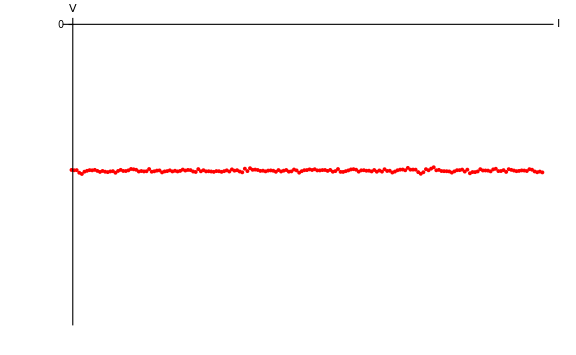

```mathematica
a5=ListPlot[all,PlotMarkers->{Automatic, 4}, PlotStyle->{Red} , PlotRange->{{755,870}, {-0.00002,0}} ,
 AxesLabel->{" I", " V"}, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"" ,Ticks->{{0,100,250,500,650,800,950,1100,1250,1400,1550,1750,1800},{0,0.00001,0.00002,0.00004,0.00007,0.00009,0.00012}},AxesOrigin->{{0},{-0,00006}}]
```

```mathematica
a55=List[{755.321,-9.90771781*^-6},{755.953,-9.89844456*^-6},{756.585,-0.0000100746363},{757.217,-0.0000101580955},{757.849,-0.0000100050808},{758.482,-9.94480475*^-6},{759.114,-9.89843853*^-6},{759.746,-9.9123484*^-6},{760.378,-9.87991325*^-6},{761.01,-9.94946271*^-6},{761.642,-0.0000100190122},{762.274,-9.95409934*^-6},{762.906,-0.0000100051023},{763.538,-0.0000100329204},{764.17,-9.98655414*^-6},{764.802,-9.96800762*^-6},{765.434,-0.0000100746501},{766.066,-9.95409277*^-6},{766.698,-9.87990673*^-6},{767.33,-9.95409277*^-6},{767.962,-9.9587294*^-6},{768.594,-9.91236312*^-6},{769.226,-9.81963638*^-6},{769.858,-9.84281954*^-6},{770.49,-9.87527595*^-6},{771.122,-9.99119171*^-6},{771.754,-9.95873301*^-6},{772.386,-9.98655279*^-6},{773.018,-9.9726429*^-6},{773.65,-9.82427076*^-6},{774.282,-0.0000100050993},{774.914,-9.97728109*^-6},{775.546,-9.93091478*^-6},{776.178,-9.91700489*^-6},{776.81,-0.0000100514672},{777.442,-9.98656382*^-6},{778.074,-9.96338065*^-6},{778.706,-9.91237767*^-6},{779.338,-9.98656382*^-6},{779.97,-9.94019748*^-6},{780.602,-9.98656164*^-6},{781.234,-9.94946857*^-6},{781.866,-9.86137254*^-6},{782.499,-9.92628541*^-6},{783.131,-9.88454011*^-6},{783.763,-9.89844999*^-6},{784.395,-9.99118252*^-6},{785.027,-0.0000100236389},{785.659,-9.82890059*^-6},{786.291,-9.97727676*^-6},{786.923,-9.9030907*^-6},{787.555,-9.98191338*^-6},{788.187,-9.97264013*^-6},{788.819,-9.99118801*^-6},{789.451,-0.0000100143712},{790.083,-9.96336823*^-6},{790.715,-9.97264149*^-6},{791.347,-0.0000100143712},{791.979,-9.96801149*^-6},{792.611,-9.91237191*^-6},{793.243,-9.99119464*^-6},{793.875,-9.84745906*^-6},{794.507,-9.93555995*^-6},{795.139,-9.90310351*^-6},{795.771,-9.99119955*^-6},{796.403,-0.0000100468392},{797.035,-9.80109757*^-6},{797.667,-9.96336536*^-6},{798.299,-9.768627*^-6},{798.931,-9.87526944*^-6},{799.562,-9.86135956*^-6},{800.194,-9.88917786*^-6},{800.826,-9.94945401*^-6},{801.458,-9.93554413*^-6},{802.09,-9.9819104*^-6},{802.722,-9.93091637*^-6},{803.354,-9.91700648*^-6},{803.986,-9.94018963*^-6},{804.618,-0.0000100097391},{805.25,-9.89382333*^-6},{805.882,-9.99120385*^-6},{806.514,-9.93556422*^-6},{807.146,-9.88919787*^-6},{807.778,-0.0000100004771},{808.41,-9.98192993*^-6},{809.042,-9.85674078*^-6},{809.674,-9.91701704*^-6},{810.306,-0.000010070026},{810.938,-9.96802003*^-6},{811.57,-9.90309341*^-6},{812.202,-9.89382015*^-6},{812.834,-9.84745386*^-6},{813.466,-9.88918352*^-6},{814.098,-9.83817061*^-6},{814.73,-9.91699324*^-6},{815.362,-9.91699324*^-6},{815.994,-9.89381011*^-6},{816.626,-9.88917349*^-6},{817.258,-9.94944763*^-6},{817.89,-9.88453489*^-6},{818.522,-0.0000100050871},{819.155,-9.96335751*^-6},{819.787,-9.82426298*^-6},{820.419,-0.0000100143646},{821.051,-0.0000100190013},{821.684,-9.96799839*^-6},{822.316,-9.9169955*^-6},{822.948,-9.85207802*^-6},{823.58,-9.83353152*^-6},{824.212,-9.87062452*^-6},{824.844,-0.00001000045},{825.476,-9.91236875*^-6},{826.108,-9.90309549*^-6},{826.74,-9.94018854*^-6},{827.372,-9.93555191*^-6},{828.004,-9.98655484*^-6},{828.636,-9.88919198*^-6},{829.268,-0.0000100051078},{829.9,-9.92164841*^-6},{830.532,-0.0000100004712},{831.164,-9.83817667*^-6},{831.796,-9.95409236*^-6},{832.428,-9.94018248*^-6},{833.06,-0.0000100607348},{833.692,-9.99582201*^-6},{834.324,-9.90772204*^-6},{834.956,-9.86599241*^-6},{835.588,-9.85671915*^-6},{836.22,-9.90772204*^-6},{836.852,-9.7454429*^-6},{837.484,-9.8659952*^-6},{838.116,-9.86135858*^-6},{838.748,-9.8659952*^-6},{839.38,-0.0000100329138},{840.012,-0.0000101442014},{840.644,-0.0000100421955},{841.276,-9.83354715*^-6},{841.908,-9.90773324*^-6},{842.54,-9.79646595*^-6},{843.172,-9.70373324*^-6},{843.804,-9.90774521*^-6},{844.436,-9.8799254*^-6},{845.068,-9.95874821*^-6},{845.7,-9.96803043*^-6},{846.332,-9.97266707*^-6},{846.964,-9.98657699*^-6},{847.596,-0.0000100653999},{848.228,-9.98192318*^-6},{848.86,-9.90310043*^-6},{849.492,-9.89846379*^-6},{850.124,-9.86137073*^-6},{850.756,-9.99583307*^-6},{851.388,-9.86597859*^-6},{852.02,-0.0000101117195},{852.652,-0.0000100282603},{853.284,-0.0000100328969},{853.916,-9.98653969*^-6},{854.548,-9.8335311*^-6},{855.18,-9.92162695*^-6},{855.812,-9.92162695*^-6},{856.442,-9.9309002*^-6},{857.074,-9.98193435*^-6},{857.706,-9.84747187*^-6},{858.338,-9.80574214*^-6},{858.97,-9.9633878*^-6},{859.602,-9.95873645*^-6},{860.234,-9.89846025*^-6},{860.866,-0.0000100190126},{861.498,-9.83354741*^-6},{862.13,-9.87991372*^-6},{862.762,-9.92625979*^-6},{863.394,-9.96798939*^-6},{864.026,-9.94944291*^-6},{864.658,-9.91698655*^-6},{865.29,-9.92627025*^-6},{865.923,-9.95872663*^-6},{866.555,-9.83353771*^-6},{867.187,-9.87063073*^-6},{867.819,-9.9865464*^-6},{868.451,-0.0000100421778},{869.083,-9.99581158*^-6},{869.715,-0.0000100514511}];
Mean[a55]
```

{812.519,-9.93777×10^-6}

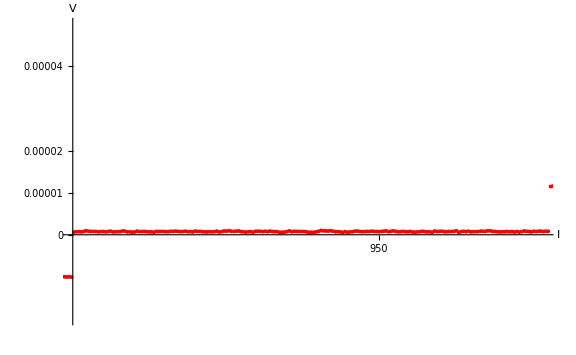

```mathematica
a6=ListPlot[all,PlotMarkers->{Automatic, 4}, PlotStyle->{Red} , PlotRange->{{870,993}, {-0.00002,0.00005}} ,
 AxesLabel->{" I", " V"}, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"" ,Ticks->{{0,100,250,500,650,800,950,1100,1250,1400,1550,1750,1800},{0,0.00001,0.00002,0.00004,0.00007,0.00009,0.00012}},AxesOrigin->{{0},{-0,00006}}]
```

```mathematica
a66=List[{869.715,-0.0000100514511},{870.347,6.49875666*^-7},{870.979,7.28698047*^-7},{871.611,7.28698047*^-7},{872.243,6.77695151*^-7},{872.875,7.79700943*^-7},{873.507,9.51256139*^-7},{874.139,8.16793577*^-7},{874.771,7.7970049*^-7},{875.403,7.84337126*^-7},{876.035,7.75063854*^-7},{876.668,6.91604728*^-7},{877.3,7.3333441*^-7},{877.932,7.7042746*^-7},{878.564,6.82331465*^-7},{879.196,7.56517566*^-7},{879.828,8.53886957*^-7},{880.46,6.8696837*^-7},{881.092,6.91604997*^-7},{881.724,7.28698016*^-7},{882.356,7.3333446*^-7},{882.988,8.95616527*^-7},{883.62,8.44613592*^-7},{884.252,6.73058264*^-7},{884.884,6.96241417*^-7},{885.516,6.12781621*^-7},{886.148,6.54511342*^-7},{886.78,8.44613404*^-7},{887.412,7.47244055*^-7},{888.044,7.70427391*^-7},{888.676,7.79700657*^-7},{889.308,7.19424432*^-7},{889.94,6.73058106*^-7},{890.572,6.9624123*^-7},{891.204,6.22055098*^-7},{891.836,7.88973894*^-7},{892.468,7.75063994*^-7},{893.1,7.65790728*^-7},{893.732,7.79700537*^-7},{894.364,7.10151011*^-7},{894.996,7.28697552*^-7},{895.627,8.16793617*^-7},{896.259,7.98247179*^-7},{896.891,8.44613507*^-7},{897.523,7.93610546*^-7},{898.155,7.28697686*^-7},{898.787,7.65790749*^-7},{899.419,8.35340131*^-7},{900.051,7.19424238*^-7},{900.683,7.33334145*^-7},{901.315,6.59147973*^-7},{901.947,8.67796546*^-7},{902.579,7.93610356*^-7},{903.211,7.98246993*^-7},{903.843,7.05514256*^-7},{904.475,6.91604345*^-7},{905.107,6.68421378*^-7},{905.739,7.10151084*^-7},{906.371,6.96241182*^-7},{907.003,7.14787718*^-7},{907.635,8.58523395*^-7},{908.267,6.45238271*^-7},{908.899,7.37970933*^-7},{909.531,9.00253093*^-7},{910.163,8.44613496*^-7},{910.795,9.55892699*^-7},{911.427,8.30703621*^-7},{912.059,7.88973929*^-7},{912.691,8.49250151*^-7},{913.323,8.95616569*^-7},{913.955,7.47244448*^-7},{914.587,7.05514789*^-7},{915.219,6.22055471*^-7},{915.851,7.05514789*^-7},{916.483,7.28697458*^-7},{917.115,6.0350827*^-7},{917.747,8.07520279*^-7},{918.379,8.39976735*^-7},{919.011,7.98246958*^-7},{919.643,7.37970668*^-7},{920.275,8.26066783*^-7},{920.907,7.37970668*^-7},{921.539,8.7243316*^-7},{922.171,7.75064447*^-7},{922.803,7.37971453*^-7},{923.435,7.42608077*^-7},{924.067,5.66416353*^-7},{924.699,5.98872588*^-7},{925.331,6.22055717*^-7},{925.963,7.56517867*^-7},{926.595,9.0952652*^-7},{927.227,7.14788234*^-7},{927.859,8.12157415*^-7},{928.491,7.75064415*^-7},{929.123,7.7042779*^-7},{929.755,7.6115454*^-7},{930.387,7.65791429*^-7},{931.019,6.86968889*^-7},{931.651,5.66416769*^-7},{932.283,5.94236489*^-7},{932.915,5.89599869*^-7},{933.547,6.68422232*^-7},{934.179,8.02884281*^-7},{934.811,1.00689567*^-6},{935.443,9.18799841*^-7},{936.075,9.09526604*^-7},{936.707,8.72433628*^-7},{937.339,9.55892824*^-7},{937.971,8.58523762*^-7},{938.603,7.19425101*^-7},{939.235,7.33334549*^-7},{939.867,6.8696826*^-7},{940.499,5.61779277*^-7},{941.131,7.42607807*^-7},{941.763,5.89598341*^-7},{942.395,6.82331077*^-7},{943.028,7.00877624*^-7},{943.659,8.30703454*^-7},{944.291,8.81706625*^-7},{944.923,7.75064115*^-7},{945.555,7.24061176*^-7},{946.187,7.42607699*^-7},{946.819,7.75064115*^-7},{947.451,7.70427688*^-7},{948.083,8.44613719*^-7},{948.715,7.84337569*^-7},{949.347,7.61154435*^-7},{949.979,7.24061387*^-7},{950.611,7.79700916*^-7},{951.243,8.35340446*^-7},{951.875,9.04889857*^-7},{952.507,7.28698015*^-7},{953.139,8.21430613*^-7},{953.771,9.18799764*^-7},{954.403,7.79700977*^-7},{955.035,6.86968452*^-7},{955.667,7.3333478*^-7},{956.299,7.98247532*^-7},{956.931,7.19424905*^-7},{957.563,6.91605154*^-7},{958.195,7.79701032*^-7},{958.828,6.40601885*^-7},{959.46,6.08145474*^-7},{960.092,6.73058295*^-7},{960.724,7.33334486*^-7},{961.356,8.26066881*^-7},{961.988,7.24060907*^-7},{962.62,6.8233119*^-7},{963.252,7.00877731*^-7},{963.884,5.71051945*^-7},{964.516,8.81706497*^-7},{965.148,7.79700518*^-7},{965.78,8.02883695*^-7},{966.412,8.39976778*^-7},{967.044,7.19424324*^-7},{967.676,7.05514421*^-7},{968.308,7.61154033*^-7},{968.94,7.65790667*^-7},{969.572,7.84337205*^-7},{970.204,9.23436226*^-7},{970.836,5.80325244*^-7},{971.468,7.28697561*^-7},{972.098,8.21430258*^-7},{972.73,7.42607368*^-7},{973.362,8.44613372*^-7},{973.994,6.91604365*^-7},{974.626,7.28697458*^-7},{975.258,7.33334094*^-7},{975.891,7.42607693*^-7},{976.523,8.39976943*^-7},{977.155,8.30703681*^-7},{977.787,8.12157157*^-7},{978.419,9.18799645*^-7},{979.051,9.2807291*^-7},{979.683,7.75064048*^-7},{980.315,7.61154152*^-7},{980.947,6.96241302*^-7},{981.579,6.73058379*^-7},{982.211,7.05514781*^-7},{982.843,7.14788039*^-7},{983.475,7.70427586*^-7},{984.107,6.962418*^-7},{984.739,7.51881298*^-7},{985.371,6.40602302*^-7},{986.003,7.61154547*^-7},{986.635,6.40602302*^-7},{987.267,7.19424599*^-7},{987.899,8.95616539*^-7},{988.531,8.07520569*^-7},{989.163,7.56517639*^-7},{989.795,6.776952*^-7},{990.427,8.26067239*^-7},{991.059,7.70427724*^-7},{991.689,8.44613744*^-7},{992.321,8.44613744*^-7},{992.953,7.61154473*^-7}];
Mean[a66]
```

{931.335,7.02108×10^-7}

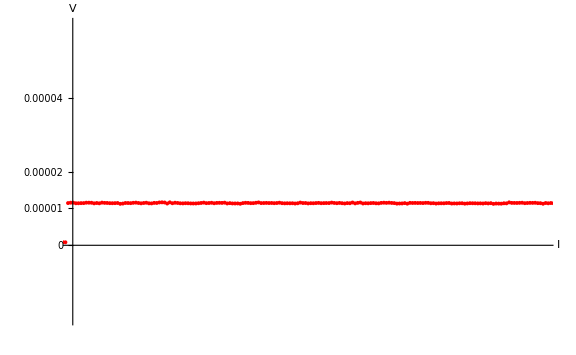

```mathematica
a7=ListPlot[all,PlotMarkers->{Automatic, 4}, PlotStyle->{Red} , PlotRange->{{996,1110}, {-0.00002,0.00006}} ,
 AxesLabel->{" I", " V"}, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"" ,Ticks->{{0,100,250,500,650,800,950,1100,1250,1400,1550,1750,1800},{0,0.00001,0.00002,0.00004,0.00007,0.00009,0.00012}},AxesOrigin->{{0},{-0,00006}}]
```

```mathematica
a77=List[{996.113,0.0000115645508},{996.746,0.0000114115413},{997.377,0.000011416178},{998.009,0.0000114486249},{998.641,0.0000114578982},{999.273,0.0000115645411},{999.905,0.0000115645411},{1000.537,0.0000115459945},{1001.169,0.0000113883423},{1001.801,0.0000114810752},{1002.433,0.0000113976156},{1003.065,0.0000115830813},{1003.697,0.0000115135415},{1004.329,0.0000114949949},{1004.961,0.0000114347185},{1005.593,0.0000114254452},{1006.225,0.0000114439918},{1006.857,0.0000114810777},{1007.489,0.0000112631554},{1008.121,0.0000113327051},{1008.753,0.0000114857144},{1009.385,0.0000114764376},{1010.017,0.0000114393445},{1010.649,0.0000115320774},{1011.281,0.0000115830804},{1011.913,0.0000114857109},{1012.545,0.000011392978},{1013.177,0.0000114857109},{1013.809,0.0000115552606},{1014.441,0.0000113976147},{1015.073,0.0000113744312},{1015.705,0.0000115135305}];
Mean[a77]
```

{1005.91,0.0000114667}

```mathematica
a8=ListPlot[all,PlotMarkers->{Automatic, 4}, PlotStyle->{Red} , PlotRange->{{1115,1310}, {-0.00002,0.00006}} ,
 AxesLabel->{" I", " V"}, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"" ,Ticks->{{0,100,250,500,650,800,950,1100,1250,1400,1550,1750,1800},{0,0.00001,0.00002,0.00004,0.00007,0.00009,0.00012}},AxesOrigin->{{0},{-0,00006}}]
```

```mathematica
a88=List[{1114.934,0.0000222335141},{1115.566,0.0000222288775},{1116.198,0.000022112961},{1116.83,0.0000221593097},{1117.462,0.0000221593097},{1118.094,0.0000221036698},{1118.726,0.000022182493},{1119.358,0.0000221036698},{1119.99,0.0000222009978},{1120.622,0.0000221870878},{1121.254,0.0000221685413},{1121.886,0.0000221917245},{1122.518,0.0000221407688},{1123.15,0.0000220990389},{1123.782,0.0000221361321},{1124.414,0.0000221732254},{1125.046,0.0000221871353},{1125.678,0.0000220434051},{1126.31,0.0000222056881},{1126.942,0.0000221964148},{1127.574,0.000022233508},{1128.207,0.0000222891143},{1128.839,0.0000222891143},{1129.471,0.0000221407416},{1130.103,0.0000220758285},{1130.735,0.000022108285},{1131.367,0.0000219738507},{1131.999,0.0000219877607},{1132.631,0.0000220526738},{1133.263,0.0000219877607},{1133.895,0.0000220526623},{1134.527,0.0000221175754},{1135.159,0.0000221175754},{1135.791,0.0000221407587},{1136.423,0.0000221314637},{1137.055,0.0000222566532},{1137.687,0.0000221175537},{1138.319,0.0000220943705},{1138.951,0.0000222010134},{1139.583,0.0000221592706},{1140.215,0.0000221592706},{1140.847,0.0000221453606},{1141.479,0.0000220340811},{1142.111,0.0000221175105},{1142.743,0.0000222102433},{1143.375,0.0000220804174},{1144.007,0.0000221314205},{1144.639,0.0000222426998},{1145.271,0.0000222890901},{1145.903,0.0000221963572},{1146.535,0.0000222659069},{1147.167,0.0000222937267},{1147.799,0.0000221824537},{1148.431,0.0000222380934},{1149.063,0.000022112904},{1149.695,0.0000221499971},{1150.327,0.0000221175406},{1150.959,0.0000219459678},{1151.591,0.0000221407068},{1152.224,0.0000220108808},{1152.856,0.0000221128869},{1153.488,0.0000222102791},{1154.12,0.0000222010058},{1154.752,0.0000221639126},{1155.384,0.0000221870958},{1156.016,0.0000220711797},{1156.648,0.0000221731769},{1157.28,0.0000221870868},{1157.912,0.0000221639036},{1158.544,0.000022145357},{1159.176,0.0000220016312},{1159.808,0.000022043361},{1160.44,0.0000221546405},{1161.072,0.0000221036374},{1161.704,0.0000221500039},{1162.336,0.0000220155436},{1162.968,0.0000220619101},{1163.6,0.0000221592796},{1164.232,0.0000221731896},{1164.864,0.0000222473691},{1165.496,0.000022275189},{1166.128,0.0000222612791},{1166.76,0.000022196366},{1167.392,0.0000219552604},{1168.024,0.000022191752},{1168.656,0.0000220109226},{1169.288,0.0000220480158},{1169.92,0.0000220294692},{1170.552,0.0000219506564},{1171.184,0.0000220665727},{1171.816,0.0000220804827},{1172.448,0.000022182489},{1173.08,0.0000222334922},{1173.712,0.0000221639284},{1174.344,0.0000221175619},{1174.976,0.0000221453818},{1175.608,0.0000220248289},{1176.24,0.0000221963824},{1176.872,0.0000221731991},{1177.504,0.0000220990127},{1178.136,0.0000220387363},{1178.768,0.0000220897394},{1179.4,0.0000220804715},{1180.032,0.0000220572882},{1180.664,0.0000221407479},{1181.296,0.0000222613008},{1181.928,0.0000223076423},{1182.56,0.000022233456},{1183.192,0.0000221731796},{1183.824,0.0000221175399},{1184.456,0.0000221824218},{1185.088,0.0000222751546},{1185.72,0.0000221406921},{1186.352,0.0000221128722},{1186.984,0.0000220479593},{1187.616,0.0000220526036},{1188.248,0.0000220155104},{1188.88,0.0000218903212},{1189.512,0.0000220433303},{1190.144,0.0000222010089},{1190.776,0.0000222798319},{1191.408,0.0000222288288},{1192.04,0.0000221917356},{1192.672,0.0000221917356},{1193.304,0.000022150025},{1193.936,0.0000220480187},{1194.568,0.0000221453884},{1195.2,0.0000221314784},{1195.832,0.0000220572901},{1196.464,0.0000220897466},{1197.096,0.0000220480168},{1197.728,0.0000220155602},{1198.36,0.000022191753},{1198.992,0.0000222705487},{1199.624,0.000022200999},{1200.256,0.0000223030052},{1200.888,0.0000221963624},{1201.52,0.0000222241892},{1202.152,0.0000222612824},{1202.784,0.0000221824594},{1203.414,0.0000221268196},{1204.046,0.0000221036364},{1204.678,0.000022052651},{1205.31,0.0000221129274},{1205.942,0.0000220341044},{1206.574,0.0000221500206},{1207.206,0.0000222149537},{1207.838,0.0000221546772},{1208.47,0.000022103674},{1209.102,0.0000220851274},{1209.734,0.0000221500405},{1210.366,0.00002217787},{1210.998,0.0000219970404},{1211.63,0.0000219924037},{1212.262,0.0000219831304},{1212.894,0.0000219042844},{1213.526,0.0000220526572},{1214.158,0.000022029474},{1214.79,0.0000220572939},{1215.422,0.00002222885},{1216.054,0.0000219738286},{1216.686,0.0000220201951},{1217.318,0.0000221871145},{1217.95,0.0000222149344},{1218.582,0.0000223401386},{1219.214,0.0000221639458},{1219.846,0.0000221407625},{1220.478,0.0000221314892},{1221.11,0.0000221036693},{1221.742,0.0000223308503},{1222.374,0.0000222102974},{1223.006,0.000022136111},{1223.638,0.0000221268377},{1224.27,0.000022177833},{1224.902,0.0000220943733},{1225.534,0.0000222427461},{1226.166,0.0000219877304},{1226.798,0.0000221268312},{1227.43,0.0000220433715},{1228.062,0.0000220990113},{1228.694,0.0000221500145},{1229.326,0.0000223864836},{1229.958,0.0000221360935},{1230.59,0.0000221917332},{1231.222,0.0000222520096},{1231.855,0.00002215464},{1232.487,0.0000222751695},{1233.119,0.0000222519863},{1233.751,0.0000222658963},{1234.383,0.0000222102566},{1235.015,0.0000222798062},{1235.647,0.0000220572561},{1236.279,0.0000221175324},{1236.911,0.0000220665294},{1237.543,0.0000221638989},{1238.175,0.0000220943611},{1238.807,0.0000221917307},{1239.439,0.0000221685474},{1240.071,0.0000221407276},{1240.703,0.0000221824574},{1241.335,0.0000221870826},{1241.967,0.0000222009925},{1242.6,0.0000222659055},{1243.232,0.0000221082597},{1243.864,0.0000221499855},{1244.497,0.0000221082558},{1245.129,0.0000222288085},{1245.762,0.0000221685321},{1246.395,0.0000222334451},{1247.028,0.0000221500029},{1247.661,0.0000222241892},{1248.294,0.0000221685495},{1248.926,0.0000220665432},{1249.559,0.0000220062676},{1250.192,0.0000219506279},{1250.825,0.0000220387242},{1251.458,0.0000219784478},{1252.091,0.0000219691745},{1252.724,0.0000220712348},{1253.357,0.0000220990547},{1253.99,0.0000221917879},{1254.623,0.0000222659744},{1255.256,0.0000221871817},{1255.889,0.0000221176317},{1256.522,0.0000222428217},{1257.155,0.000022154725},{1257.788,0.0000219924418},{1258.421,0.0000221639563},{1259.054,0.0000220480399},{1259.687,0.00002197849},{1260.32,0.0000219877633},{1260.953,0.000022006297},{1261.586,0.0000221685799},{1262.219,0.0000220665735},{1262.852,0.0000222613129},{1263.485,0.0000221917632},{1264.117,0.0000220434127},{1264.749,0.0000220990526},{1265.382,0.0000219924094},{1266.015,0.0000219970461},{1266.647,0.0000219645858},{1267.279,0.000022163962},{1267.912,0.0000221825087},{1268.545,0.0000222335119},{1269.178,0.000022340155},{1269.81,0.0000221824908},{1270.443,0.000022205674},{1271.076,0.0000221083043},{1271.709,0.0000220619378},{1272.342,0.0000219831018},{1272.975,0.0000220155583},{1273.607,0.0000221453846},{1274.24,0.0000221963877},{1274.873,0.0000220943409},{1275.506,0.0000220108814},{1276.138,0.0000220665211},{1276.771,0.0000219598783},{1277.404,0.0000221221608},{1278.037,0.0000221685721},{1278.669,0.0000221407522},{1279.302,0.0000222427586},{1279.935,0.0000222010287},{1280.568,0.0000222242171},{1281.201,0.0000220665709},{1281.834,0.000022024841},{1282.467,0.0000219923844},{1283.099,0.0000220433876},{1283.732,0.0000220943665},{1284.365,0.0000219969969},{1284.998,0.0000220804566},{1285.631,0.0000220340901},{1286.264,0.0000222242115},{1286.897,0.0000221268418},{1287.53,0.0000220665654},{1288.163,0.0000220480187},{1288.796,0.000022085112},{1289.428,0.0000221407939},{1290.061,0.0000221454305},{1290.693,0.0000221593405},{1291.325,0.0000220805173},{1291.957,0.0000220897916},{1292.589,0.0000220248784},{1293.221,0.0000220990649},{1293.853,0.0000221407949},{1294.485,0.0000220851549},{1295.117,0.0000220433778},{1295.749,0.0000220480145},{1296.381,0.0000220248312},{1297.013,0.0000219970113},{1297.645,0.000022265909},{1298.277,0.0000222705456},{1298.909,0.0000221824494},{1299.541,0.0000221592662},{1300.173,0.0000221499929},{1300.805,0.000022247346},{1301.437,0.0000221407033},{1302.069,0.0000222102529},{1302.701,0.0000221731598},{1303.333,0.0000220757939},{1303.965,0.0000219923343},{1304.597,0.0000221036137},{1305.229,0.0000220062443},{1305.861,0.0000219645145},{1306.494,0.0000220943683},{1307.126,0.0000221731913},{1307.758,0.0000221129149},{1308.39,0.0000220758217},{1309.022,0.0000221314747},{1309.654,0.0000221175648},{1310.286,0.0000221732046}];
Mean[a88]
```

{1212.59,0.0000221304}

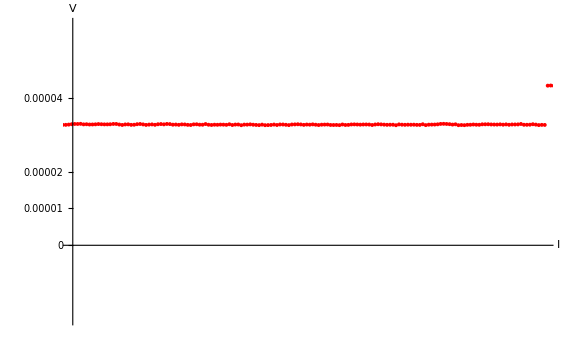

```mathematica
a9=ListPlot[all,PlotMarkers->{Automatic, 4}, PlotStyle->{Red} , PlotRange->{{1320,1420}, {-0.00002,0.00006}} ,
 AxesLabel->{" I", " V"}, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"" ,Ticks->{{0,100,250,500,650,800,950,1100,1250,1400,1550,1750,1800},{0,0.00001,0.00002,0.00004,0.00007,0.00009,0.00012}},AxesOrigin->{{0},{-0,00006}}]
```

```mathematica
a99=List[{1320.397,0.0000329440986},{1321.029,0.000032939462},{1321.661,0.0000329811917},{1322.293,0.0000328374558},{1322.925,0.0000328698787},{1323.557,0.0000327956924},{1324.189,0.0000328096024},{1324.821,0.0000328466955},{1325.453,0.000032916245},{1326.085,0.0000328698968},{1326.717,0.0000328328037},{1327.349,0.0000328374403},{1327.955,0.0000328606235},{1328.613,0.0000329487526},{1329.245,0.000032944116},{1329.877,0.0000327911066},{1330.509,0.0000326798271},{1331.141,0.0000328142899},{1331.773,0.0000328374479},{1332.405,0.0000327076219},{1333.037,0.0000327354417},{1333.669,0.0000328791776},{1334.301,0.000032939437},{1334.933,0.000032823521},{1335.565,0.0000326890584},{1336.197,0.000032772518},{1336.829,0.000032823521},{1337.461,0.0000327169075},{1338.093,0.0000328652801},{1338.725,0.0000329209198},{1339.357,0.0000328374602},{1339.989,0.0000329487425},{1340.621,0.0000329116494},{1341.253,0.0000327540034},{1341.885,0.0000327864599},{1342.517,0.0000327122736},{1343.149,0.0000328282002},{1343.781,0.0000328096536},{1344.413,0.0000327076474},{1345.046,0.0000326659176},{1345.678,0.0000328328175},{1346.31,0.0000328560007},{1346.942,0.0000327493579},{1347.574,0.0000327400846},{1348.206,0.0000329209137},{1348.838,0.0000327354195},{1349.47,0.0000326751432},{1350.102,0.0000327446928},{1350.734,0.0000327215096},{1351.366,0.0000327725031},{1351.998,0.0000327585932},{1352.63,0.0000327122268},{1353.262,0.0000328605992},{1353.894,0.0000326658604},{1354.526,0.0000327817914},{1355.158,0.0000327957014},{1355.79,0.0000326102358},{1356.422,0.0000327678815},{1357.054,0.0000327633678},{1357.686,0.000032828281},{1358.318,0.0000327401845},{1358.95,0.0000326845446},{1359.582,0.0000326335583},{1360.214,0.0000327633848},{1360.846,0.0000326150117},{1361.478,0.0000326428316},{1362.111,0.0000326752883},{1362.744,0.0000327818366},{1363.376,0.0000326659204},{1364.008,0.0000328003831},{1364.64,0.0000327957465},{1365.272,0.0000327215309},{1365.904,0.0000326380713},{1366.536,0.0000327957172},{1367.168,0.000032823537},{1367.8,0.0000328606302},{1368.432,0.0000328096608},{1369.064,0.0000327030179},{1369.696,0.0000327864775},{1370.328,0.0000327493843},{1370.96,0.0000328281826},{1371.592,0.0000327400864},{1372.224,0.0000326566268},{1372.856,0.0000327493597},{1373.488,0.0000327725429},{1374.12,0.0000327863954},{1374.752,0.0000326751162},{1375.384,0.0000326658429},{1376.016,0.0000326797528},{1376.648,0.0000326287891},{1377.28,0.0000328003448},{1377.912,0.0000326705189},{1378.544,0.0000326983387},{1379.176,0.0000328096181},{1379.808,0.0000328282006},{1380.441,0.0000327957441},{1381.073,0.0000327586509},{1381.705,0.0000328003807},{1382.337,0.0000328049614},{1382.969,0.0000327817782},{1383.601,0.0000326658622},{1384.233,0.0000328003247},{1384.865,0.0000328698743},{1385.497,0.0000328234786},{1386.129,0.0000327632024},{1386.761,0.000032716836},{1387.393,0.0000327400192},{1388.025,0.0000327446987},{1388.657,0.0000326055995},{1389.289,0.0000328235216},{1389.921,0.0000327493354},{1390.553,0.0000327168789},{1391.185,0.0000327493631},{1391.817,0.0000327354532},{1392.449,0.0000327493631},{1393.081,0.0000327029967},{1393.713,0.0000326936904},{1394.345,0.000032865246},{1394.977,0.000032633414},{1395.609,0.0000327539667},{1396.241,0.0000327725132},{1396.873,0.0000327864125},{1397.505,0.0000328466888},{1398.137,0.0000329579681},{1398.769,0.0000329811513},{1399.401,0.0000329440461},{1400.033,0.0000328884065},{1400.664,0.0000327771272},{1401.296,0.0000328513134},{1401.928,0.0000326148449},{1402.56,0.0000326612805},{1403.192,0.0000326195507},{1403.824,0.0000327122836},{1404.456,0.0000327308302},{1405.088,0.0000327957799},{1405.72,0.0000327401401},{1406.352,0.0000327262301},{1406.984,0.0000328467831},{1407.616,0.0000328514197},{1408.248,0.000032865271},{1408.88,0.0000328049946},{1409.512,0.0000327864481},{1410.144,0.0000327771748},{1410.776,0.0000328328132},{1411.408,0.0000327539903},{1412.04,0.0000328281766},{1412.672,0.0000327261704},{1413.304,0.0000328049915},{1413.936,0.0000328049915},{1414.568,0.0000328235381},{1415.2,0.0000329394542},{1415.832,0.0000327308052},{1416.464,0.0000327262114},{1417.096,0.0000327493946},{1417.728,0.0000328699475},{1418.36,0.0000327679412},{1418.992,0.0000326427338},{1419.624,0.0000327030102},{1420.256,0.0000326844636}];
Mean[a99]
```

{1370.33,0.0000327782}

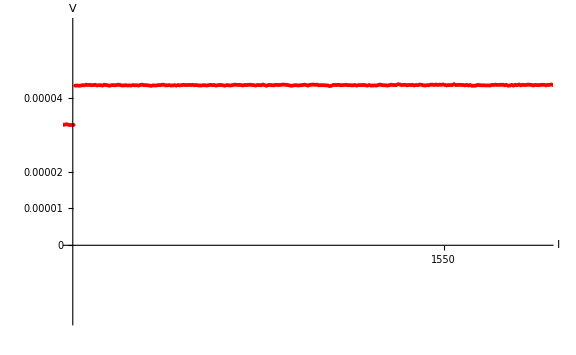

```mathematica
a10=ListPlot[all,PlotMarkers->{Automatic, 4}, PlotStyle->{Red} , PlotRange->{{1420,1585}, {-0.00002,0.00006}} ,
 AxesLabel->{" I", " V"}, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"" ,Ticks->{{0,100,250,500,650,800,950,1100,1250,1400,1550,1750,1800},{0,0.00001,0.00002,0.00004,0.00007,0.00009,0.00012}},AxesOrigin->{{0},{-0,00006}}]
```

```mathematica
a100=List[{1420.256,0.0000326844636},{1420.888,0.0000433487502},{1421.52,0.0000433858434},{1422.152,0.0000433301476},{1422.784,0.0000433718774},{1423.416,0.0000434785201},{1424.048,0.0000434321537},{1424.68,0.0000435898193},{1425.312,0.000043515633},{1425.945,0.0000435666361},{1426.577,0.0000434692666},{1427.209,0.0000435063597},{1427.841,0.0000435759586},{1428.473,0.0000434136759},{1429.106,0.000043464679},{1429.738,0.0000434878622},{1430.37,0.0000433719485},{1431.002,0.0000435805977},{1431.634,0.0000435249579},{1432.266,0.0000434368616},{1432.898,0.0000433255821},{1433.53,0.0000434739745},{1434.16,0.0000435017944},{1434.792,0.0000434461546},{1435.424,0.0000435064311},{1436.056,0.000043608462},{1436.688,0.0000434925456},{1437.32,0.0000433951759},{1437.952,0.0000434090859},{1438.584,0.0000434600891},{1439.217,0.000043390529},{1439.85,0.0000434229855},{1440.482,0.000043390529},{1441.114,0.0000434925353},{1441.746,0.0000434369292},{1442.378,0.0000434601125},{1443.01,0.0000433766527},{1443.642,0.0000435342989},{1444.274,0.0000436316687},{1444.906,0.0000434925665},{1445.538,0.0000434832932},{1446.17,0.0000434415633},{1446.802,0.0000433859234},{1447.434,0.0000433023967},{1448.066,0.0000434183129},{1448.698,0.0000433997663},{1449.33,0.0000433997663},{1449.962,0.0000434924993},{1450.594,0.000043483258},{1451.226,0.0000435899009},{1451.858,0.0000436084475},{1452.49,0.0000434276181},{1453.122,0.0000434415299},{1453.754,0.0000434832598},{1454.384,0.0000433951634},{1455.014,0.0000433998},{1455.646,0.0000434878964},{1456.278,0.0000433672997},{1456.91,0.0000434971258},{1457.542,0.0000434183028},{1458.174,0.0000434924892},{1458.806,0.0000435713887},{1459.438,0.0000435157488},{1460.07,0.0000434972022},{1460.702,0.0000435435687},{1461.334,0.0000435157065},{1461.966,0.0000435713463},{1462.598,0.0000434647033},{1463.23,0.0000435017965},{1463.862,0.0000434322468},{1464.494,0.0000433997606},{1465.126,0.0000433904873},{1465.758,0.0000434785836},{1466.39,0.0000434368538},{1467.022,0.0000433997381},{1467.654,0.000043478561},{1468.286,0.000043557384},{1468.918,0.0000434924709},{1469.55,0.0000435202908},{1470.182,0.0000433765603},{1470.814,0.0000434553833},{1471.446,0.0000435388429},{1472.078,0.0000434971131},{1472.71,0.0000434322524},{1473.342,0.0000433487927},{1473.974,0.0000435018022},{1474.606,0.0000434322524},{1475.238,0.0000433997958},{1475.87,0.0000434600976},{1476.502,0.0000435899239},{1477.134,0.0000436084705},{1477.766,0.0000435435574},{1478.398,0.0000435482479},{1479.03,0.0000435018813},{1479.662,0.0000434091481},{1480.294,0.0000435436112},{1480.926,0.0000434972446},{1481.558,0.000043571339},{1482.19,0.0000435945222},{1482.822,0.0000435296091},{1483.454,0.0000434832426},{1484.086,0.0000433811991},{1484.718,0.0000435156618},{1485.35,0.0000434832053},{1485.982,0.000043473932},{1486.614,0.0000436362146},{1487.246,0.0000434971343},{1487.878,0.0000433209417},{1488.51,0.0000435017709},{1489.142,0.0000435295908},{1489.774,0.0000434785594},{1490.406,0.0000434275563},{1491.038,0.0000435805656},{1491.67,0.0000435388358},{1492.302,0.0000435202892},{1492.934,0.0000435620709},{1493.566,0.0000436501673},{1494.198,0.0000436130741},{1494.83,0.0000435759809},{1495.46,0.0000435018357},{1496.092,0.0000433859193},{1496.724,0.0000433302795},{1497.356,0.0000434137393},{1497.988,0.0000434647425},{1498.62,0.0000434323196},{1499.252,0.0000434044997},{1499.884,0.0000434647762},{1500.516,0.0000435157795},{1501.148,0.0000436131547},{1501.78,0.0000435296948},{1502.412,0.0000433674118},{1503.044,0.0000435575148},{1503.676,0.000043608518},{1504.308,0.0000436548738},{1504.94,0.0000435667773},{1505.572,0.0000436224172},{1506.204,0.0000434554975},{1506.836,0.0000434786434},{1507.468,0.0000434693701},{1508.1,0.0000434693701},{1508.732,0.0000434090936},{1509.364,0.0000434090588},{1509.997,0.0000432421394},{1510.629,0.0000433163258},{1511.261,0.0000435296117},{1511.893,0.000043538885},{1512.525,0.0000435111066},{1513.158,0.0000435945664},{1513.791,0.0000434740134},{1514.422,0.0000434693767},{1515.054,0.0000435157426},{1515.686,0.0000435760191},{1516.318,0.0000434786494},{1516.95,0.0000434879227},{1517.582,0.0000434276462},{1518.214,0.0000434275961},{1518.846,0.0000435296024},{1519.478,0.0000433719563},{1520.11,0.0000434878725},{1520.742,0.0000434878456},{1521.374,0.0000435017555},{1522.006,0.0000435388487},{1522.638,0.0000434507524},{1523.27,0.0000433580195},{1523.902,0.0000435156816},{1524.534,0.0000433580356},{1525.167,0.0000433997654},{1525.799,0.000043404402},{1526.431,0.0000433812141},{1527.063,0.0000435110402},{1527.695,0.0000436501396},{1528.327,0.0000435203135},{1528.959,0.0000434507638},{1529.591,0.0000434461071},{1530.223,0.0000433719208},{1530.855,0.0000434507438},{1531.487,0.000043603753},{1532.119,0.000043543512},{1532.751,0.0000435064188},{1533.383,0.0000435064188},{1534.015,0.0000437336146},{1534.647,0.0000436501549},{1535.279,0.0000435110624},{1535.911,0.0000435574289},{1536.543,0.0000435713389},{1537.175,0.0000434600593},{1537.807,0.000043529647},{1538.439,0.0000435111004},{1539.071,0.0000435574669},{1539.703,0.000043409094},{1540.335,0.000043515737},{1540.968,0.0000434879206},{1541.6,0.0000436362935},{1542.232,0.0000435945636},{1542.864,0.000043441554},{1543.496,0.0000433951193},{1544.128,0.0000434693056},{1544.76,0.0000434600323},{1545.392,0.000043608405},{1546.024,0.0000436223149},{1546.656,0.0000435203612},{1547.288,0.0000436501874},{1547.92,0.0000435342711},{1548.552,0.0000436130942},{1549.184,0.0000435898734},{1549.814,0.0000436686964},{1550.446,0.0000435342336},{1551.078,0.0000434322274},{1551.71,0.0000434925038},{1552.342,0.000043510957},{1552.974,0.0000435202303},{1553.606,0.0000437520622},{1554.238,0.0000435202303},{1554.87,0.0000435387417},{1555.502,0.0000435711981},{1556.134,0.0000435526516},{1556.766,0.0000435248317},{1557.398,0.0000434368546},{1558.03,0.0000435434975},{1558.662,0.0000434090347},{1559.294,0.0000435110409},{1559.926,0.0000433163018},{1560.558,0.0000433488195},{1561.19,0.0000433488195},{1561.822,0.0000435389223},{1562.454,0.0000434740091},{1563.086,0.0000434461455},{1563.718,0.0000434368722},{1564.35,0.0000434368722},{1564.956,0.000043399779},{1565.614,0.0000434229623},{1566.246,0.0000433951901},{1566.878,0.0000435528364},{1567.51,0.0000435389264},{1568.142,0.0000436223862},{1568.774,0.0000435528464},{1569.406,0.0000435667564},{1570.038,0.000043571393},{1570.67,0.0000436177596},{1571.303,0.00004345084},{1571.935,0.0000435667411},{1572.567,0.0000433441818},{1573.199,0.0000433859116},{1573.831,0.0000435528312},{1574.463,0.0000433674038},{1575.095,0.0000435853267},{1575.727,0.0000434740469},{1576.359,0.0000436502399},{1576.991,0.0000434508636},{1577.623,0.0000435713921},{1578.255,0.0000435342989},{1578.887,0.0000435435722},{1579.519,0.000043627032},{1580.151,0.0000436037438},{1580.783,0.0000435434675},{1581.415,0.0000434090048},{1582.047,0.0000435527408},{1582.679,0.0000435017377},{1583.311,0.0000434692009},{1583.943,0.0000435665703},{1584.575,0.0000435851168},{1585.207,0.0000435804802}];
Mean[a100]
```

{1502.73,0.0000434497}

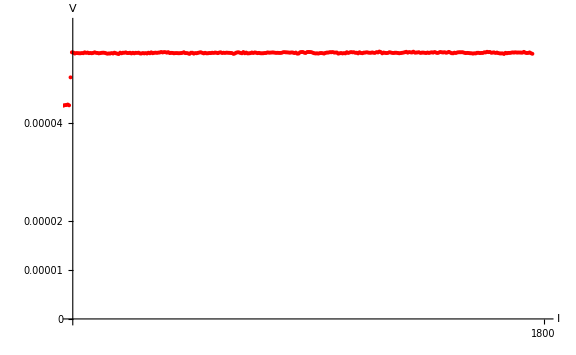

```mathematica
a11=ListPlot[all,PlotMarkers->{Automatic, 4}, PlotStyle->{Red} , PlotRange->{{1590,1800}, {0,0.00006}} ,
 AxesLabel->{" I", " V"}, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"" ,Ticks->{{0,100,250,500,650,800,950,1100,1250,1400,1550,1750,1800},{0,0.00001,0.00002,0.00004,0.00007,0.00009,0.00012}},AxesOrigin->{{0},{-0,00006}}]
```

```mathematica
a110=List[{1590.263,0.0000542587866},{1590.895,0.0000540501375},{1591.527,0.0000541429148},{1592.157,0.0000541336415},{1592.787,0.0000541011849},{1593.417,0.0000541011849},{1594.047,0.0000541429148},{1594.679,0.0000541197845},{1595.311,0.0000543006141},{1595.943,0.0000541893343},{1596.575,0.0000542542475},{1597.207,0.0000541244432},{1597.839,0.0000541661731},{1598.471,0.0000541105332},{1599.103,0.0000541800831},{1599.735,0.0000543052713},{1600.367,0.0000542032648},{1600.999,0.0000541708082},{1601.631,0.0000540873484},{1602.263,0.0000541383516},{1602.895,0.0000542031661},{1603.527,0.000054230986},{1604.159,0.0000542031661},{1604.791,0.0000541104331},{1605.423,0.0000540223707},{1606.055,0.0000540733739},{1606.687,0.0000540548273},{1607.319,0.0000541429237},{1607.951,0.000054059464},{1608.583,0.0000542264283},{1609.215,0.0000541105119},{1609.847,0.0000540316888},{1610.479,0.0000539575023},{1611.111,0.0000542309982},{1611.743,0.000054101172},{1612.375,0.0000542217249},{1613.007,0.0000542124516},{1613.639,0.000054286638},{1614.271,0.000054156865},{1614.903,0.000054156865},{1615.535,0.0000542125049},{1616.167,0.0000540734053},{1616.799,0.0000542079092},{1617.431,0.0000540919927},{1618.063,0.0000542079092},{1618.695,0.0000541847259},{1619.327,0.0000542310925},{1619.959,0.0000540780347},{1620.591,0.0000540548514},{1621.223,0.0000541475845},{1621.855,0.0000540780347},{1622.487,0.0000541337082},{1623.119,0.0000540595217},{1623.751,0.0000542218047},{1624.383,0.0000541058883},{1625.015,0.0000542959912},{1625.647,0.0000541151111},{1626.279,0.0000542032075},{1626.911,0.0000542403008},{1627.543,0.0000541985709},{1628.175,0.0000542449033},{1628.807,0.0000542634499},{1629.439,0.0000543608196},{1630.071,0.0000542680866},{1630.703,0.0000543376363},{1631.335,0.0000543236946},{1631.967,0.0000542309617},{1632.599,0.0000543376046},{1633.231,0.0000541428654},{1633.863,0.0000541984553},{1634.495,0.0000541845454},{1635.127,0.0000540964492},{1635.759,0.0000541381789},{1636.391,0.0000541428156},{1637.023,0.0000541104048},{1637.655,0.0000541150415},{1638.287,0.0000541428614},{1638.919,0.0000541985011},{1639.551,0.0000543190599},{1640.183,0.0000541382306},{1640.815,0.0000541428673},{1641.447,0.0000540825909},{1642.079,0.0000539898579},{1642.711,0.0000542170666},{1643.343,0.0000542170666},{1643.975,0.0000540316007},{1644.607,0.0000541382436},{1645.239,0.0000541104249},{1645.871,0.0000541985212},{1646.503,0.0000542680709},{1647.135,0.0000543051641},{1647.767,0.0000541985344},{1648.399,0.0000540826182},{1649.031,0.000054203171},{1649.663,0.0000540965281},{1650.295,0.0000541011647},{1650.927,0.0000541660924},{1651.559,0.0000541475458},{1652.191,0.0000542217322},{1652.823,0.0000541800023},{1653.455,0.0000542541772},{1654.087,0.000054217084},{1654.719,0.0000541336243},{1655.351,0.0000542495406},{1655.983,0.0000543005437},{1656.615,0.0000541614182},{1657.247,0.0000542263312},{1657.879,0.0000541799648},{1658.511,0.0000542356045},{1659.143,0.0000542170419},{1659.775,0.0000541984954},{1660.407,0.0000541753121},{1661.039,0.000054138219},{1661.671,0.0000539852097},{1662.303,0.0000540687104},{1662.935,0.0000542309931},{1663.567,0.0000543051795},{1664.199,0.0000542773596},{1664.831,0.0000541753732},{1665.461,0.0000541058235},{1666.093,0.0000543562026},{1666.725,0.0000541104601},{1667.357,0.0000542495596},{1667.989,0.0000540826666},{1668.621,0.0000540965766},{1669.253,0.0000541336698},{1669.885,0.0000542634961},{1670.517,0.0000541615454},{1671.149,0.0000542774618},{1671.781,0.0000542264586},{1672.413,0.0000541290888},{1673.045,0.0000541893653},{1673.677,0.0000541104999},{1674.309,0.0000540965899},{1674.941,0.0000541058632},{1675.573,0.0000541568664},{1676.205,0.0000541613654},{1676.837,0.0000542819181},{1677.469,0.0000542355516},{1678.101,0.0000542355516},{1678.733,0.0000542633715},{1679.365,0.0000542772007},{1679.997,0.000054235471},{1680.629,0.0000541937413},{1681.261,0.0000542076512},{1681.893,0.0000541937807},{1682.525,0.0000541798707},{1683.157,0.0000542030539},{1683.789,0.0000543096966},{1684.421,0.0000543328798},{1685.053,0.0000542911786},{1685.685,0.0000542865419},{1686.317,0.0000542540854},{1686.949,0.0000542309022},{1687.581,0.0000542818482},{1688.213,0.0000542493917},{1688.845,0.0000541520223},{1689.477,0.0000542540283},{1690.109,0.0000540407431},{1690.741,0.0000540546775},{1691.373,0.000054305056},{1692.005,0.0000543560591},{1692.637,0.0000543606957},{1693.269,0.0000542262519},{1693.901,0.0000541706122},{1694.533,0.0000543514412},{1695.165,0.0000543746244},{1695.797,0.0000543514412},{1696.429,0.0000543328732},{1697.061,0.0000542169573},{1697.693,0.0000541149512},{1698.325,0.0000540639482},{1698.957,0.0000540964408},{1699.589,0.0000540454378},{1700.221,0.0000541335339},{1700.853,0.0000541567172},{1701.485,0.0000541103482},{1702.117,0.0000540454352},{1702.749,0.0000541938078},{1703.381,0.0000542540841},{1704.013,0.0000542448108},{1704.645,0.0000543282899},{1705.277,0.0000543051067},{1705.909,0.0000543468365},{1706.541,0.0000542541036},{1707.173,0.0000542541214},{1707.805,0.000054258758},{1708.437,0.0000540361991},{1709.069,0.0000541057488},{1709.701,0.0000541567518},{1710.333,0.0000540686717},{1710.965,0.0000541335847},{1711.597,0.0000540825816},{1712.229,0.0000543236872},{1712.861,0.0000541753977},{1713.493,0.0000542727674},{1714.125,0.0000543423172},{1714.757,0.000054291314},{1715.389,0.0000543144973},{1716.021,0.0000542078706},{1716.653,0.0000542217806},{1717.285,0.000054082681},{1717.917,0.0000543145137},{1718.549,0.0000541614617},{1719.181,0.0000541150951},{1719.813,0.0000542402847},{1720.445,0.0000542449214},{1721.077,0.0000543051978},{1721.709,0.0000542542277},{1722.341,0.0000542124978},{1722.973,0.0000542124978},{1723.605,0.000054277411},{1724.237,0.0000542078124},{1724.869,0.0000541939025},{1725.501,0.0000543422753},{1726.133,0.0000542680889},{1726.765,0.0000544581915},{1727.397,0.000054342202},{1728.029,0.0000540918233},{1728.661,0.0000542587425},{1729.293,0.0000541938294},{1729.925,0.0000541520917},{1730.557,0.0000541845482},{1731.189,0.0000543097375},{1731.821,0.0000542680078},{1732.453,0.0000541938215},{1733.085,0.0000541613447},{1733.717,0.0000542262576},{1734.349,0.0000542169843},{1734.981,0.0000541706179},{1735.613,0.0000541011213},{1736.245,0.0000541428511},{1736.877,0.0000542031275},{1737.509,0.0000542448573},{1738.141,0.0000543144069},{1738.773,0.0000544071538},{1739.405,0.0000542263246},{1740.037,0.0000543468774},{1740.669,0.0000542912376},{1741.301,0.0000542633996},{1741.933,0.0000544303188},{1742.565,0.0000542355797},{1743.197,0.0000542494897},{1743.829,0.0000542773095},{1744.461,0.0000543144877},{1745.093,0.0000541800248},{1745.725,0.0000542403012},{1746.357,0.0000542495745},{1746.989,0.0000542078469},{1747.621,0.0000541614804},{1748.253,0.0000542634868},{1748.885,0.0000541753904},{1749.517,0.000054254231},{1750.149,0.0000543005976},{1750.781,0.0000542356844},{1751.413,0.0000543562374},{1752.045,0.0000542449577},{1752.677,0.0000541708496},{1753.309,0.0000542543095},{1753.941,0.0000543609527},{1754.573,0.0000543006761},{1755.205,0.0000542635826},{1755.837,0.0000543192226},{1756.469,0.0000542218527},{1757.101,0.000054258946},{1757.733,0.0000543887725},{1758.365,0.0000542636046},{1758.997,0.0000541152314},{1759.629,0.0000540966848},{1760.261,0.0000542357846},{1760.893,0.0000541661449},{1761.525,0.0000542727879},{1762.157,0.0000543098812},{1762.789,0.0000543052445},{1763.421,0.0000543145178},{1764.053,0.0000543005747},{1764.685,0.0000542124783},{1765.291,0.0000541429286},{1765.949,0.0000541846584},{1766.581,0.0000541615321},{1767.213,0.0000541058922},{1767.845,0.0000541058922},{1768.477,0.000054040979},{1769.109,0.0000540966189},{1769.742,0.0000540780325},{1770.373,0.0000542078588},{1771.005,0.0000542078588},{1771.637,0.000054138309},{1772.269,0.0000541800122},{1772.901,0.0000541753755},{1773.533,0.0000543005651},{1774.165,0.0000542727452},{1774.797,0.0000544072081},{1775.429,0.0000543375996},{1776.061,0.0000543700561},{1776.693,0.0000542077735},{1777.325,0.00005425414},{1777.957,0.0000542819579},{1778.589,0.000054175315},{1779.221,0.000054254138},{1779.853,0.0000541335852},{1780.485,0.0000540733088},{1781.115,0.0000540733685},{1781.747,0.0000540872785},{1782.379,0.0000539667255},{1783.011,0.0000541985581},{1783.643,0.0000541058414},{1784.275,0.0000541846645},{1784.907,0.0000541846645},{1785.54,0.0000542263943},{1786.172,0.0000542866708},{1786.804,0.0000542449493},{1787.436,0.0000543005892},{1788.068,0.000054249586},{1788.7,0.0000542634959},{1789.332,0.0000542588717},{1789.964,0.0000542495984},{1790.596,0.0000542310518},{1791.228,0.0000543933347},{1791.86,0.0000542310518},{1792.492,0.0000541568301},{1793.124,0.0000541800134},{1793.756,0.0000542820197},{1794.388,0.0000541151003},{1795.021,0.0000540037644}];
Mean[a110]
```

{1692.64,0.000054202}

```mathematica
av=List[{115.41817037037036,-0.00005269580804333331},{340.0963399209486,-0.000041949612506324104},{554.9787920792079,-0.000031297048582178227},{704.1305806451612,-0.00002061780561096774},{812.5187857142856,-9.937765701263741*^-6},{931.3352040816327,7.02108257959184*^-7},{1005.90903125,0.000011466734546874997},{1212.5931000000003,0.000022130436837096782},{1370.326955974843,0.00003277819738679246},{1502.7306793893126,0.00004344974470190833},{1692.6376769230774,0.000054202046947692316}]
```

{{115.418,-0.0000526958},{340.096,-0.0000419496},{554.979,-0.000031297},{704.131,-0.0000206178},{812.519,-9.93777×10^-6},{931.335,7.02108×10^-7},{1005.91,0.0000114667},{1212.59,0.0000221304},{1370.33,0.0000327782},{1502.73,0.0000434497},{1692.64,0.000054202}}

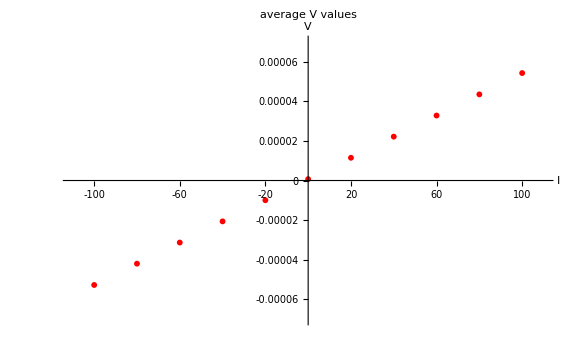

```mathematica
tot=List[{-100,-0.00005269580804333331},{-80,-0.000041949612506324104},{-60,-0.000031297048582178227},{-40,-0.00002061780561096774},{-20,-9.937765701263741*^-6},{0,7.02108257959184*^-7},{20,0.000011466734546874997},{40,0.000022130436837096782},{60,0.00003277819738679246},{80,0.00004344974470190833},{100,0.000054202046947692316}];


atot=ListPlot[tot,PlotMarkers->{Automatic, 6}, PlotStyle->{Red} , PlotRange->{{-110,110}, {-0.00007,0.00007}} ,
 AxesLabel->{" I", " V"}, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"average V values " ,Ticks->{{-100,-80,-60,-40,-20,0,20,40,60,80,100},{-0.00006,-0.00005,-0.00004,-0.00003,-0.00002,-0.00001,0,0.00001,0.00002,0.00003,0.00004,0.00005,0.00006}}]
```

```mathematica
fito=LinearModelFit[tot,x,x]
```

FittedModel[7.48293×10^-7+5.34188×10^-7 x]

```mathematica
%3["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 7.48293×10^-7 | 9.22132×10^-9 | 81.1482 | 3.31846×10^-14
x | 5.34188×10^-7 | 1.45802×10^-10 | 3663.79 | 4.28048×10^-29

```mathematica
%3["AdjustedRSquared"]
```

0.999999

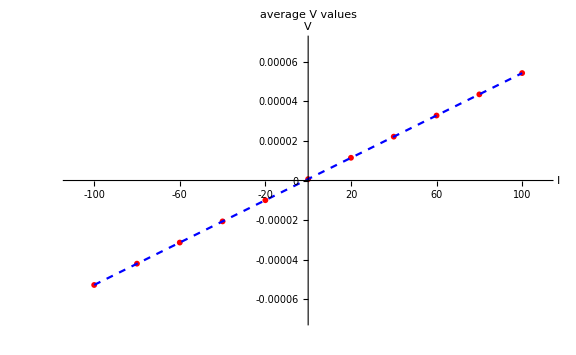

```mathematica
final=Show[atot,Plot[{ 7.482934758415421*^-7+5.341879212905625*^-7 x},{x,-100,100} , PlotStyle->{Blue, Dashed} ]]
```

```mathematica
Calculating the resisitivities
```

```mathematica
l=48.8;
dl=2;
d=0.1111;
dd=0.0015;
b=15.28;
db=0.09;
A=d*b;
x=5.341879212905625*^-7;
dx=1.4580192813507004*^-10;
Solve[ ro*l/A==x,ro]
dro=Sqrt[ (( b* x*dd/l)^2  )   +       (( d* x*db/l)^2  )   +      (( A* x*dl/(l^2))^2  )   + (dx*A/l)^2]
```

{{ro→1.85828×10^-8}}

8.09305×10^-10

```mathematica
x100m=-0.00005269580804333331/(-100);
x80m=-0.000041949612506324104/(-80);
x60m= -0.000031297048582178227/(-60);
x40m=-0.00002061780561096774/(-40);
x20m= -9.937765701263741*^-6/(-20);
x20=0.000011466734546874997/20;
x40=0.000022130436837096782/40;
x60=0.00003277819738679246/60;
x80=0.00004344974470190833/80;
x100=0.000054202046947692316/100;



dro100min=Sqrt[ (( b* x100m*dd/l)^2  )   +       (( d* x100m*db/l)^2  )   +      (( A* x100m*dl/(l^2))^2  )   ]
dro80min=Sqrt[ ( b* x80m*dd/l)^2     +       ( d* x80m*db/l)^2     +      ( A* x80m*dl/l^2)^2     ]
dro60min=Sqrt[ ( b* x60m*dd/l)^2     +       ( d* x60m*db/l)^2     +      ( A* x60m*dl/l^2)^2     ]
dro40min=Sqrt[ ( b* x40m*dd/l)^2     +       ( d* x40m*db/l)^2     +      ( A* x40m*dl/l^2)^2     ]
dro20min=Sqrt[ ( b* x20m*dd/l)^2     +       ( d* x20m*db/l)^2     +      ( A* x20m*dl/l^2)^2     ]
dro20=Sqrt[ ( b* x20*dd/l)^2     +       ( d* x20*db/l)^2     +      ( A* x20*dl/l^2)^2     ]
dro40=Sqrt[ ( b* x40*dd/l)^2     +       ( d* x40*db/l)^2     +      ( A* x40*dl/l^2)^2     ]
dro60=Sqrt[ ( b* x60*dd/l)^2     +       ( d* x60*db/l)^2     +      ( A* x60*dl/l^2)^2     ]
dro80=Sqrt[ ( b* x80*dd/l)^2     +       ( d* x80*db/l)^2     +      ( A* x80*dl/l^2)^2     ]
dro100=Sqrt[ ( b* x100*dd/l)^2     +       ( d* x100*db/l)^2     +      ( A* x100*dl/l^2)^2     ]
```

7.98336×10^-10

7.94415×10^-10

7.90245×10^-10

7.80894×10^-10

7.5278×10^-10

8.68599×10^-10

8.38184×10^-10

8.27643×10^-10

8.22824×10^-10

8.21155×10^-10

```mathematica
Solve[ ro*l/A==x100m,ro]
Solve[ ro*l/A==x80m,ro]
Solve[ ro*l/A==x60m,ro]
Solve[ ro*l/A==x40m,ro]
Solve[ ro*l/A==x20m,ro]
Solve[ ro*l/A==x20,ro]
Solve[ ro*l/A==x40,ro]
Solve[ ro*l/A==x60,ro]
Solve[ ro*l/A==x80,ro]
Solve[ ro*l/A==x100,ro]
```

{{ro→1.83313×10^-8}}

{{ro→1.82413×10^-8}}

{{ro→1.81455×10^-8}}

{{ro→1.79308×10^-8}}

{{ro→1.72853×10^-8}}

{{ro→1.99447×10^-8}}

{{ro→1.92463×10^-8}}

{{ro→1.90043×10^-8}}

{{ro→1.88936×10^-8}}

{{ro→1.88553×10^-8}}

```mathematica
Averaging the resistivity values for each current correctly
```

```mathematica
ro100=(-(1.833131666000553*^-8) + (1.8855292728438127*^-8))/2
```

2.61988×10^-10

```mathematica
ro80=(-1.824129041691492*^-8+ 1.8893605072724694*^-8)/2
```

3.26157×10^-10

```mathematica
ro60=(-1.814553280378908*^-8 + 1.90042794089474*^-8)/2
```

4.29373×10^-10

```mathematica
ro40=(-1.793081544447937*^-8 + 1.9246314865855637*^-8)/2
```

6.5775×10^-10

```mathematica
ro20=(-1.7285277209621865*^-8+ 1.994469293099526*^-8)/2
```

1.32971×10^-9

```mathematica
res=List[{20,1.3297078606866967*^-9},{40,6.577497106881343*^-10},{60,4.293733025791607*^-10},{80,3.2615732790488627*^-10},{100,2.6198803421629835*^-10}]
```

{{20,1.32971×10^-9},{40,6.5775×10^-10},{60,4.29373×10^-10},{80,3.26157×10^-10},{100,2.61988×10^-10}}

```mathematica
d100=Sqrt[(7.983357181615528*^-10)^2  + (8.211550725292756*^-10)^2] /2
d80=Sqrt[(7.94415041498543*^-10)^2  + (8.228235894971374*^-10)^2] /2
d60=Sqrt[(7.902447615201799*^-10)^2  + (8.276434983628861*^-10)^2] /2
d40=Sqrt[(7.808937399637056*^-10)^2  + (8.381842333190919*^-10)^2] /2
d20=Sqrt[(7.527803076399877*^-10)^2  + (8.685988600762596*^-10)^2] /2
```

5.72633×10^-10

5.71868×10^-10

5.72163×10^-10

5.72789×10^-10

5.74705×10^-10

```mathematica
f3=LinearModelFit[res,Exp[x^-1],x]
```

FittedModel[-2.59605×10^-8+2.59591×10^-8 ⅇ^(1/x)]

```mathematica
f3["AdjustedRSquared"]
```

0.999927

```mathematica
Needs["ErrorBarPlots`"]
erresis=ErrorListPlot[ {{{20,1.3297078606866967*^-9} ,ErrorBar[0,5.74704744041741*^-10]}  ,{{40,6.577497106881343*^-10},ErrorBar[0,5.727887573310115*^-10]},{{60,4.293733025791607*^-10},ErrorBar[0,5.721626830483709*^-10]},{{80,3.2615732790488627*^-10},ErrorBar[0,5.718684109111303*^-10]},{{100,2.6198803421629835*^-10},ErrorBar[0,5.726332971529603*^-10]}}, AxesLabel->{"I (mV)", "ρ (Ωm)"}, LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio,    PlotStyle->Directive[Thin,PointSize[Large],Red,"LineColor"->Green], LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.01]]]
```

-Graphics-

```mathematica
f4=LinearModelFit[res,x^-1,x]
```

FittedModel[-1.02659×10^-11+(2.67706×10^-8)/x]

```mathematica
f4["AdjustedRSquared"]
```

0.999876

```mathematica
final4=Show[erresis,Plot[{-1.0265921865867008*^-11+(2.6770562149528567*^-8)/x},{x,0,100} , PlotStyle->{Blue, Dashed, Thin}],PlotLabel->"ρ = -1.0266·10^-11    +(2.6771·10^-8)/I"  ]
```

-Graphics-